```mathematica
ClearAll["Global`*"]
```

Define colors for graphs

```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
```

## System Description

The system consists of two individual thermal transistors S1 and S2, connected in a Darlington pair configuration. 
S1 - Connected to three thermal baths, B_HOT (collector), B_CNT (base) and B_INT (emitter)
S2 - Connected to three thermal baths, B_HOT (collector), B_INT (base) and B_COL (emitter)

The thermal bath B_HOT is at a high temperature, while B_COL is at a low temperature. The temperature T_CNT of control terminal  B_CNT can be varied.
The temperature T_INT of the intermediate bath B_INT is not controllable, but is determined by the thermal equilibrium condition.

In this context, the thermal equilibrium condition would be that heat inflow to the bath B_INT from S1 should match the heat outflow to S2 from bath B_INT.

Each transistor is modelled individually using the techniques developed for Optically Controlled Quantum Thermal Gate paper.

## Deriving the quantum master equation for a single transistor or a single optical gate

The index S represents which transistor is considered.

Eigenstates,
|1> =|+z,+z,+z>
|2> =|+z,+z,-z>
|3> =|+z,-z,+z>
|4> =|+z,-z,-z>
|5> =|-z,+z,+z>
|6> =|-z,+z,-z>
|7> =|-z,-z,+z>
|8> =|-z,-z,-z>

### Density matrix

```mathematica
Subscript[ρMatrix, S_][t_]:=Table[Subscript[ρ, S,i,j][t],{i,1,8},{j,1,8}];
MatrixForm[Subscript[ρMatrix, 1][t]]
```

(ρ_(1,1,1)[t] | ρ_(1,1,2)[t] | ρ_(1,1,3)[t] | ρ_(1,1,4)[t] | ρ_(1,1,5)[t] | ρ_(1,1,6)[t] | ρ_(1,1,7)[t] | ρ_(1,1,8)[t]
ρ_(1,2,1)[t] | ρ_(1,2,2)[t] | ρ_(1,2,3)[t] | ρ_(1,2,4)[t] | ρ_(1,2,5)[t] | ρ_(1,2,6)[t] | ρ_(1,2,7)[t] | ρ_(1,2,8)[t]
ρ_(1,3,1)[t] | ρ_(1,3,2)[t] | ρ_(1,3,3)[t] | ρ_(1,3,4)[t] | ρ_(1,3,5)[t] | ρ_(1,3,6)[t] | ρ_(1,3,7)[t] | ρ_(1,3,8)[t]
ρ_(1,4,1)[t] | ρ_(1,4,2)[t] | ρ_(1,4,3)[t] | ρ_(1,4,4)[t] | ρ_(1,4,5)[t] | ρ_(1,4,6)[t] | ρ_(1,4,7)[t] | ρ_(1,4,8)[t]
ρ_(1,5,1)[t] | ρ_(1,5,2)[t] | ρ_(1,5,3)[t] | ρ_(1,5,4)[t] | ρ_(1,5,5)[t] | ρ_(1,5,6)[t] | ρ_(1,5,7)[t] | ρ_(1,5,8)[t]
ρ_(1,6,1)[t] | ρ_(1,6,2)[t] | ρ_(1,6,3)[t] | ρ_(1,6,4)[t] | ρ_(1,6,5)[t] | ρ_(1,6,6)[t] | ρ_(1,6,7)[t] | ρ_(1,6,8)[t]
ρ_(1,7,1)[t] | ρ_(1,7,2)[t] | ρ_(1,7,3)[t] | ρ_(1,7,4)[t] | ρ_(1,7,5)[t] | ρ_(1,7,6)[t] | ρ_(1,7,7)[t] | ρ_(1,7,8)[t]
ρ_(1,8,1)[t] | ρ_(1,8,2)[t] | ρ_(1,8,3)[t] | ρ_(1,8,4)[t] | ρ_(1,8,5)[t] | ρ_(1,8,6)[t] | ρ_(1,8,7)[t] | ρ_(1,8,8)[t])

### System Hamiltonian

```mathematica
Subscript[HsMatrix, S_]:=({{1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]+Subscript[ωM, S]+Subscript[ωMR, S]+Subscript[ωR, S]+Subscript[ωRL, S]), 0, 0, 0, 0, 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]+Subscript[ωM, S]-Subscript[ωMR, S]-Subscript[ωR, S]-Subscript[ωRL, S]), 0, 0, 0, 0, 0, 0}, {0, 0, 1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]-Subscript[ωM, S]-Subscript[ωMR, S]+Subscript[ωR, S]+Subscript[ωRL, S]), 0, 0, 0, 0, 0}, {0, 0, 0, 1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]-Subscript[ωM, S]+Subscript[ωMR, S]-Subscript[ωR, S]-Subscript[ωRL, S]), 0, 0, 0, 0}, {0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]-Subscript[ωM, S]-Subscript[ωMR, S]-Subscript[ωR, S]+Subscript[ωRL, S]), 0, 0, 0}, {0, 0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]+Subscript[ωLM, S]-Subscript[ωM, S]+Subscript[ωMR, S]+Subscript[ωR, S]-Subscript[ωRL, S]), 0, 0}, {0, 0, 0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]+Subscript[ωM, S]+Subscript[ωMR, S]-Subscript[ωR, S]+Subscript[ωRL, S]), 0}, {0, 0, 0, 0, 0, 0, 0, -1/2 ℏ (Subscript[ωL, S]-Subscript[ωLM, S]+Subscript[ωM, S]-Subscript[ωMR, S]+Subscript[ωR, S]-Subscript[ωRL, S])}})
```

```mathematica
Subscript[HsEVal, S_][i_]:=(Eigenvalues[Subscript[HsMatrix, S]][[{8,1,7,2,4,5,3,6}]])[[i]]
Subscript[HsEVec, S_][i_]:=(Eigenvectors[Subscript[HsMatrix, S]][[{8,1,7,2,4,5,3,6}]])[[i]]
```

Relation between eigenvalues and ωs

```mathematica
ωassum=Flatten[{Table[Subscript[ω, S,i,j]->(Subscript[HsEVal, S][i]-Subscript[HsEVal, S][j] )/ℏ,{S,1,2},{i,1,8},{j,1,8}]}];
```

### Interaction Hamiltonian with the classically modelled optical field

Ω_P represents the strength of the interaction between the device P and the optical field

```mathematica
Subscript[HlMatrix, S_]:= ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, S])/2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, S])/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -(ℏ Subscript[Ω, S])/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -(ℏ Subscript[Ω, S])/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

Net optical field induced decaying rate Υ_P[i,j] of the device P from state | i > to state | j > while absorbing energy from the external electric field.
Υs[i,j] is used due to variable naming issues.

```mathematica
Subscript[Υs, S_][i_,j_]:= Subscript[Ω, S]/2 ⅈ(Subscript[ρ, S,i,j][t]-Subscript[ρ, S,j,i][t])
```

### Lindblad terms from environment interactions

Taking results from the previous work (“Optically Controlled Quantum Thermal Gate”)

```mathematica
temp1=({{-Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,1}][t]+Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {1,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {1,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {1,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {1,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {1,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {1,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {1,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {2,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,1}][t], -Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,2}][t]+Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {2,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {2,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {2,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {2,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {2,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {2,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {3,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {3,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,2}][t], -Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,3}][t]+Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {3,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {3,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {3,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {3,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {3,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {4,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {4,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {4,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,3}][t], -Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,4}][t]+Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,8}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {4,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {4,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {4,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {4,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {5,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {5,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {5,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {5,4}][t], Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {1,1}][t]-Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {5,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {5,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {5,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {5,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {6,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {6,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {6,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {6,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {6,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,5}][t], Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {2,2}][t]-Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {6,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {6,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {6,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {7,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {7,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {7,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {7,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {7,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {7,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,6}][t], Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {3,3}][t]-Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,7}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {7,8}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {7,8}][t]}, {-1/2 Subscript[J, 1][Subscript[ω, {5,1}]] Subscript[NBE, 1][Subscript[ω, {5,1}]] Subscript[ρ, {8,1}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,1}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] Subscript[NBE, 1][Subscript[ω, {6,2}]] Subscript[ρ, {8,2}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,2}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] Subscript[NBE, 1][Subscript[ω, {7,3}]] Subscript[ρ, {8,3}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,3}][t], -1/2 Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {8,4}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,4}][t], -1/2 Subscript[J, 1][Subscript[ω, {5,1}]] (1+Subscript[NBE, 1][Subscript[ω, {5,1}]]) Subscript[ρ, {8,5}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,5}][t], -1/2 Subscript[J, 1][Subscript[ω, {6,2}]] (1+Subscript[NBE, 1][Subscript[ω, {6,2}]]) Subscript[ρ, {8,6}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,6}][t], -1/2 Subscript[J, 1][Subscript[ω, {7,3}]] (1+Subscript[NBE, 1][Subscript[ω, {7,3}]]) Subscript[ρ, {8,7}][t]-1/2 Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,7}][t], Subscript[J, 1][Subscript[ω, {8,4}]] Subscript[NBE, 1][Subscript[ω, {8,4}]] Subscript[ρ, {4,4}][t]-Subscript[J, 1][Subscript[ω, {8,4}]] (1+Subscript[NBE, 1][Subscript[ω, {8,4}]]) Subscript[ρ, {8,8}][t]}});
temp2=({{-Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,1}][t]+Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {1,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {1,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {1,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {1,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {1,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {1,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {1,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {2,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,1}][t], -Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,2}][t]+Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {2,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {2,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {2,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {2,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {2,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {2,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {3,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {3,2}][t], Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {1,1}][t]-Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {3,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {3,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {3,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {3,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {3,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {3,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {4,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {4,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {4,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,3}][t], Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {2,2}][t]-Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {4,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {4,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {4,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {4,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {4,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {5,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {5,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {5,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {5,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,4}][t], -Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,5}][t]+Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {5,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {5,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {5,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {6,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {6,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {6,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {6,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {6,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,5}][t], -Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,6}][t]+Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,8}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {6,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {6,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {7,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {7,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {7,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {7,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {7,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {7,6}][t], Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {5,5}][t]-Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,7}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {7,8}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {7,8}][t]}, {-1/2 Subscript[J, 2][Subscript[ω, {3,1}]] Subscript[NBE, 2][Subscript[ω, {3,1}]] Subscript[ρ, {8,1}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,1}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] Subscript[NBE, 2][Subscript[ω, {4,2}]] Subscript[ρ, {8,2}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,2}][t], -1/2 Subscript[J, 2][Subscript[ω, {3,1}]] (1+Subscript[NBE, 2][Subscript[ω, {3,1}]]) Subscript[ρ, {8,3}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,3}][t], -1/2 Subscript[J, 2][Subscript[ω, {4,2}]] (1+Subscript[NBE, 2][Subscript[ω, {4,2}]]) Subscript[ρ, {8,4}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,4}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] Subscript[NBE, 2][Subscript[ω, {7,5}]] Subscript[ρ, {8,5}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,5}][t], -1/2 Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {8,6}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,6}][t], -1/2 Subscript[J, 2][Subscript[ω, {7,5}]] (1+Subscript[NBE, 2][Subscript[ω, {7,5}]]) Subscript[ρ, {8,7}][t]-1/2 Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,7}][t], Subscript[J, 2][Subscript[ω, {8,6}]] Subscript[NBE, 2][Subscript[ω, {8,6}]] Subscript[ρ, {6,6}][t]-Subscript[J, 2][Subscript[ω, {8,6}]] (1+Subscript[NBE, 2][Subscript[ω, {8,6}]]) Subscript[ρ, {8,8}][t]}});
temp3=({{-Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,1}][t]+Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {1,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {1,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {1,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {1,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {1,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {1,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {1,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {2,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,1}][t], Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {1,1}][t]-Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {2,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {2,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {2,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {2,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {2,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {2,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {2,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {3,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {3,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,2}][t], -Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,3}][t]+Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {3,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {3,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {3,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {3,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {3,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {4,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {4,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {4,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,3}][t], Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {3,3}][t]-Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {4,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {4,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {4,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {4,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {4,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {5,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {5,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {5,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {5,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,4}][t], -Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,5}][t]+Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {5,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {5,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {5,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {6,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {6,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {6,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {6,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {6,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,5}][t], Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {5,5}][t]-Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {6,7}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {6,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {6,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {7,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {7,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {7,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {7,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {7,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {7,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,6}][t], -Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,7}][t]+Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,8}][t], -1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,8}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {7,8}][t]}, {-1/2 Subscript[J, 3][Subscript[ω, {2,1}]] Subscript[NBE, 3][Subscript[ω, {2,1}]] Subscript[ρ, {8,1}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,1}][t], -1/2 Subscript[J, 3][Subscript[ω, {2,1}]] (1+Subscript[NBE, 3][Subscript[ω, {2,1}]]) Subscript[ρ, {8,2}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,2}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] Subscript[NBE, 3][Subscript[ω, {4,3}]] Subscript[ρ, {8,3}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,3}][t], -1/2 Subscript[J, 3][Subscript[ω, {4,3}]] (1+Subscript[NBE, 3][Subscript[ω, {4,3}]]) Subscript[ρ, {8,4}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,4}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] Subscript[NBE, 3][Subscript[ω, {6,5}]] Subscript[ρ, {8,5}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,5}][t], -1/2 Subscript[J, 3][Subscript[ω, {6,5}]] (1+Subscript[NBE, 3][Subscript[ω, {6,5}]]) Subscript[ρ, {8,6}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,6}][t], -1/2 Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {8,7}][t]-1/2 Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,7}][t], Subscript[J, 3][Subscript[ω, {8,7}]] Subscript[NBE, 3][Subscript[ω, {8,7}]] Subscript[ρ, {7,7}][t]-Subscript[J, 3][Subscript[ω, {8,7}]] (1+Subscript[NBE, 3][Subscript[ω, {8,7}]]) Subscript[ρ, {8,8}][t]}});
```

```mathematica
temp1/.{Subscript[J, i_]-> Subscript[J, S,i],Subscript[ω, {i_,j_}]-> Subscript[ω, S,i,j],Subscript[ρ, {i_,j_}]->Subscript[ρ, S,i,j],Subscript[NBE, i_]->Subscript[NBE, S,i]}//MatrixForm
temp2/.{Subscript[J, i_]-> Subscript[J, S,i],Subscript[ω, {i_,j_}]-> Subscript[ω, S,i,j],Subscript[ρ, {i_,j_}]->Subscript[ρ, S,i,j],Subscript[NBE, i_]->Subscript[NBE, S,i]}//MatrixForm
temp3/.{Subscript[J, i_]-> Subscript[J, S,i],Subscript[ω, {i_,j_}]-> Subscript[ω, S,i,j],Subscript[ρ, {i_,j_}]->Subscript[ρ, S,i,j],Subscript[NBE, i_]->Subscript[NBE, S,i]}//MatrixForm
```

(-J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,1)[t]+J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,5)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,2)[t]-1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,1,2)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,1,3)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,1,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,5)[t]-1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,1,5)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,6)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,1,6)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,1,7)[t] | -1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,1,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,2,1)[t]-1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,1)[t] | -J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,2)[t]+J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,6)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,2,3)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,2,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,2,5)[t]-1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,6)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,2,6)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,2,7)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,2,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,3,1)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,3,2)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,2)[t] | -J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,3)[t]+J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,7)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,3,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,3,5)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,3,6)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,6)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,3,7)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,3,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,4,1)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,4,2)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,2)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,4,3)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,3)[t] | -J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,4)[t]+J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,8)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,4,5)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,4,6)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,6)[t] | -1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,4,7)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,7)[t] | -1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,4,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,5,1)[t]-1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,1)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,2)[t]-1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,5,2)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,5,3)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,5,4)[t] | J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,1,1)[t]-J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,5)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,6)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,5,6)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,5,7)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,5,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,5,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,6,1)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,6,2)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,2)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,6,3)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,6,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,6,5)[t]-1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,5)[t] | J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,2,2)[t]-J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,6)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,7)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,6,7)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,6,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,6,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,7,1)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,7,2)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,2)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,7,3)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,3)[t] | -1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,7,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,7,5)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,7,6)[t]-1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,6)[t] | J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,3,3)[t]-J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,7)[t] | -1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,7,8)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,7,8)[t]
-1/2 J_(S,1)[ω_(S,5,1)] NBE_(S,1)[ω_(S,5,1)] ρ_(S,8,1)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,1)[t] | -1/2 J_(S,1)[ω_(S,6,2)] NBE_(S,1)[ω_(S,6,2)] ρ_(S,8,2)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,2)[t] | -1/2 J_(S,1)[ω_(S,7,3)] NBE_(S,1)[ω_(S,7,3)] ρ_(S,8,3)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,3)[t] | -1/2 J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,8,4)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,4)[t] | -1/2 J_(S,1)[ω_(S,5,1)] (1+NBE_(S,1)[ω_(S,5,1)]) ρ_(S,8,5)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,5)[t] | -1/2 J_(S,1)[ω_(S,6,2)] (1+NBE_(S,1)[ω_(S,6,2)]) ρ_(S,8,6)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,6)[t] | -1/2 J_(S,1)[ω_(S,7,3)] (1+NBE_(S,1)[ω_(S,7,3)]) ρ_(S,8,7)[t]-1/2 J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,7)[t] | J_(S,1)[ω_(S,8,4)] NBE_(S,1)[ω_(S,8,4)] ρ_(S,4,4)[t]-J_(S,1)[ω_(S,8,4)] (1+NBE_(S,1)[ω_(S,8,4)]) ρ_(S,8,8)[t])

(-J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,1)[t]+J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,3)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,1,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,3)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,1,3)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,1,4)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,1,5)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,1,6)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,1,7)[t] | -1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,1,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,2,1)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,1)[t] | -J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,2)[t]+J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,4)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,2,3)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,2,4)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,2,5)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,2,6)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,2,7)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,2,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,3,1)[t]-1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,1)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,3,2)[t] | J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,1,1)[t]-J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,3)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,4)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,3,4)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,3,5)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,3,6)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,3,7)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,3,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,3,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,4,1)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,4,2)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,4,3)[t]-1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,3)[t] | J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,2,2)[t]-J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,4)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,4,5)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,4,6)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,4,7)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,4,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,4,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,5,1)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,5,2)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,5,3)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,5,4)[t]-1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,4)[t] | -J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,5)[t]+J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,7)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,5,6)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,7)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,5,7)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,5,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,6,1)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,6,2)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,6,3)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,6,4)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,4)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,6,5)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,5)[t] | -J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,6)[t]+J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,8)[t] | -1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,6,7)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,7)[t] | -1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,6,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,7,1)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,7,2)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,7,3)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,7,4)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,4)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,7,5)[t]-1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,5)[t] | -1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,7,6)[t] | J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,5,5)[t]-J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,7)[t] | -1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,7,8)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,7,8)[t]
-1/2 J_(S,2)[ω_(S,3,1)] NBE_(S,2)[ω_(S,3,1)] ρ_(S,8,1)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,1)[t] | -1/2 J_(S,2)[ω_(S,4,2)] NBE_(S,2)[ω_(S,4,2)] ρ_(S,8,2)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,2)[t] | -1/2 J_(S,2)[ω_(S,3,1)] (1+NBE_(S,2)[ω_(S,3,1)]) ρ_(S,8,3)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,3)[t] | -1/2 J_(S,2)[ω_(S,4,2)] (1+NBE_(S,2)[ω_(S,4,2)]) ρ_(S,8,4)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,4)[t] | -1/2 J_(S,2)[ω_(S,7,5)] NBE_(S,2)[ω_(S,7,5)] ρ_(S,8,5)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,5)[t] | -1/2 J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,8,6)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,6)[t] | -1/2 J_(S,2)[ω_(S,7,5)] (1+NBE_(S,2)[ω_(S,7,5)]) ρ_(S,8,7)[t]-1/2 J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,7)[t] | J_(S,2)[ω_(S,8,6)] NBE_(S,2)[ω_(S,8,6)] ρ_(S,6,6)[t]-J_(S,2)[ω_(S,8,6)] (1+NBE_(S,2)[ω_(S,8,6)]) ρ_(S,8,8)[t])

(-J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,1)[t]+J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,2)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,2)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,1,2)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,1,3)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,1,4)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,1,5)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,1,6)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,1,7)[t] | -1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,1,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,2,1)[t]-1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,1)[t] | J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,1,1)[t]-J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,2)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,2,3)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,2,4)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,2,5)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,2,6)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,2,7)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,2,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,2,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,3,1)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,3,2)[t]-1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,2)[t] | -J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,3)[t]+J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,4)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,4)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,3,4)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,3,5)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,3,6)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,3,7)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,3,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,4,1)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,4,2)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,4,3)[t]-1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,3)[t] | J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,3,3)[t]-J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,4)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,4,5)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,4,6)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,4,7)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,4,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,4,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,5,1)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,5,2)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,5,3)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,3)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,5,4)[t]-1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,4)[t] | -J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,5)[t]+J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,6)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,6)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,5,6)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,5,7)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,5,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,6,1)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,6,2)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,6,3)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,3)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,6,4)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,4)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,6,5)[t]-1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,5)[t] | J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,5,5)[t]-J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,6)[t] | -1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,6,7)[t] | -1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,6,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,6,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,7,1)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,7,2)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,7,3)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,3)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,7,4)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,4)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,7,5)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,5)[t] | -1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,7,6)[t]-1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,6)[t] | -J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,7)[t]+J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,8)[t] | -1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,8)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,7,8)[t]
-1/2 J_(S,3)[ω_(S,2,1)] NBE_(S,3)[ω_(S,2,1)] ρ_(S,8,1)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,1)[t] | -1/2 J_(S,3)[ω_(S,2,1)] (1+NBE_(S,3)[ω_(S,2,1)]) ρ_(S,8,2)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,2)[t] | -1/2 J_(S,3)[ω_(S,4,3)] NBE_(S,3)[ω_(S,4,3)] ρ_(S,8,3)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,3)[t] | -1/2 J_(S,3)[ω_(S,4,3)] (1+NBE_(S,3)[ω_(S,4,3)]) ρ_(S,8,4)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,4)[t] | -1/2 J_(S,3)[ω_(S,6,5)] NBE_(S,3)[ω_(S,6,5)] ρ_(S,8,5)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,5)[t] | -1/2 J_(S,3)[ω_(S,6,5)] (1+NBE_(S,3)[ω_(S,6,5)]) ρ_(S,8,6)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,6)[t] | -1/2 J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,8,7)[t]-1/2 J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,7)[t] | J_(S,3)[ω_(S,8,7)] NBE_(S,3)[ω_(S,8,7)] ρ_(S,7,7)[t]-J_(S,3)[ω_(S,8,7)] (1+NBE_(S,3)[ω_(S,8,7)]) ρ_(S,8,8)[t])

Linbladian for the Markovian quantum master equation,

```mathematica
Subscript[LinMatrix, S_,1]:=({{-Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,1][t]+Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,1,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,1,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,1,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,1,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,1,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,1,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,1,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,2,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,1][t], -Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,2][t]+Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,2,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,2,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,2,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,2,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,2,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,2,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,3,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,3,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,2][t], -Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,3][t]+Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,3,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,3,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,3,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,3,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,3,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,4,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,4,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,4,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,3][t], -Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,4][t]+Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,8][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,4,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,4,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,4,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,4,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,5,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,5,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,5,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,5,4][t], Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,1,1][t]-Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,5,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,5,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,5,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,5,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,6,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,6,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,6,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,6,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,6,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,5][t], Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,2,2][t]-Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,6,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,6,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,6,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,7,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,7,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,7,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,7,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,7,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,7,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,6][t], Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,3,3][t]-Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,7][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,7,8][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,7,8][t]}, {-1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] Subscript[NBE, S,1][Subscript[ω, S,5,1]] Subscript[ρ, S,8,1][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,1][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] Subscript[NBE, S,1][Subscript[ω, S,6,2]] Subscript[ρ, S,8,2][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,2][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] Subscript[NBE, S,1][Subscript[ω, S,7,3]] Subscript[ρ, S,8,3][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,3][t], -1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,8,4][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,4][t], -1/2 Subscript[J, S,1][Subscript[ω, S,5,1]] (1+Subscript[NBE, S,1][Subscript[ω, S,5,1]]) Subscript[ρ, S,8,5][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,5][t], -1/2 Subscript[J, S,1][Subscript[ω, S,6,2]] (1+Subscript[NBE, S,1][Subscript[ω, S,6,2]]) Subscript[ρ, S,8,6][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,6][t], -1/2 Subscript[J, S,1][Subscript[ω, S,7,3]] (1+Subscript[NBE, S,1][Subscript[ω, S,7,3]]) Subscript[ρ, S,8,7][t]-1/2 Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,7][t], Subscript[J, S,1][Subscript[ω, S,8,4]] Subscript[NBE, S,1][Subscript[ω, S,8,4]] Subscript[ρ, S,4,4][t]-Subscript[J, S,1][Subscript[ω, S,8,4]] (1+Subscript[NBE, S,1][Subscript[ω, S,8,4]]) Subscript[ρ, S,8,8][t]}})
Subscript[LinMatrix, S_,2]:=({{-Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,1][t]+Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,1,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,1,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,1,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,1,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,1,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,1,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,1,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,2,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,1][t], -Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,2][t]+Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,2,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,2,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,2,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,2,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,2,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,2,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,3,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,3,2][t], Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,1,1][t]-Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,3,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,3,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,3,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,3,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,3,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,3,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,4,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,4,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,4,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,3][t], Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,2,2][t]-Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,4,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,4,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,4,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,4,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,4,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,5,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,5,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,5,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,5,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,4][t], -Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,5][t]+Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,5,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,5,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,5,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,6,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,6,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,6,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,6,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,6,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,5][t], -Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,6][t]+Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,8][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,6,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,6,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,7,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,7,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,7,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,7,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,7,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,7,6][t], Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,5,5][t]-Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,7][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,7,8][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,7,8][t]}, {-1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] Subscript[NBE, S,2][Subscript[ω, S,3,1]] Subscript[ρ, S,8,1][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,1][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] Subscript[NBE, S,2][Subscript[ω, S,4,2]] Subscript[ρ, S,8,2][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,2][t], -1/2 Subscript[J, S,2][Subscript[ω, S,3,1]] (1+Subscript[NBE, S,2][Subscript[ω, S,3,1]]) Subscript[ρ, S,8,3][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,3][t], -1/2 Subscript[J, S,2][Subscript[ω, S,4,2]] (1+Subscript[NBE, S,2][Subscript[ω, S,4,2]]) Subscript[ρ, S,8,4][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,4][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] Subscript[NBE, S,2][Subscript[ω, S,7,5]] Subscript[ρ, S,8,5][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,5][t], -1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,8,6][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,6][t], -1/2 Subscript[J, S,2][Subscript[ω, S,7,5]] (1+Subscript[NBE, S,2][Subscript[ω, S,7,5]]) Subscript[ρ, S,8,7][t]-1/2 Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,7][t], Subscript[J, S,2][Subscript[ω, S,8,6]] Subscript[NBE, S,2][Subscript[ω, S,8,6]] Subscript[ρ, S,6,6][t]-Subscript[J, S,2][Subscript[ω, S,8,6]] (1+Subscript[NBE, S,2][Subscript[ω, S,8,6]]) Subscript[ρ, S,8,8][t]}})
Subscript[LinMatrix, S_,3]:=({{-Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,1][t]+Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,1,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,1,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,1,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,1,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,1,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,1,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,1,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,2,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,1][t], Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,1,1][t]-Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,2,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,2,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,2,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,2,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,2,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,2,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,2,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,3,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,3,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,2][t], -Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,3][t]+Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,3,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,3,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,3,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,3,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,3,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,4,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,4,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,4,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,3][t], Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,3,3][t]-Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,4,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,4,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,4,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,4,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,4,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,5,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,5,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,5,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,5,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,4][t], -Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,5][t]+Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,5,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,5,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,5,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,6,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,6,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,6,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,6,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,6,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,5][t], Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,5,5][t]-Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,6,7][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,6,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,6,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,7,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,7,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,7,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,7,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,7,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,7,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,6][t], -Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,7][t]+Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,8][t], -1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,8][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,7,8][t]}, {-1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] Subscript[NBE, S,3][Subscript[ω, S,2,1]] Subscript[ρ, S,8,1][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,1][t], -1/2 Subscript[J, S,3][Subscript[ω, S,2,1]] (1+Subscript[NBE, S,3][Subscript[ω, S,2,1]]) Subscript[ρ, S,8,2][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,2][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] Subscript[NBE, S,3][Subscript[ω, S,4,3]] Subscript[ρ, S,8,3][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,3][t], -1/2 Subscript[J, S,3][Subscript[ω, S,4,3]] (1+Subscript[NBE, S,3][Subscript[ω, S,4,3]]) Subscript[ρ, S,8,4][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,4][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] Subscript[NBE, S,3][Subscript[ω, S,6,5]] Subscript[ρ, S,8,5][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,5][t], -1/2 Subscript[J, S,3][Subscript[ω, S,6,5]] (1+Subscript[NBE, S,3][Subscript[ω, S,6,5]]) Subscript[ρ, S,8,6][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,6][t], -1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,8,7][t]-1/2 Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,7][t], Subscript[J, S,3][Subscript[ω, S,8,7]] Subscript[NBE, S,3][Subscript[ω, S,8,7]] Subscript[ρ, S,7,7][t]-Subscript[J, S,3][Subscript[ω, S,8,7]] (1+Subscript[NBE, S,3][Subscript[ω, S,8,7]]) Subscript[ρ, S,8,8][t]}})
```

Net thermal decaying rate Τ_(S,P)[i,j] of component S from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_(S,P)[i,j] is used due to variable naming issues.

```mathematica
Subscript[Τs, S_,P_][i_,j_]:=Subscript[J, S,P][Subscript[ω, S,i,j]]((1+Subscript[NBE, S,P][Subscript[ω, S,i,j]])Subscript[ρ, S,i,i][t]-Subscript[NBE, S,P][Subscript[ω, S,i,j]]Subscript[ρ, S,j,j][t])
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, 1,1],
Flatten[Table[Subscript[Τs, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, 1,2],
Flatten[Table[Subscript[Τs, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]

ReplaceArithmetically[Subscript[LinMatrix, 1,3],
Flatten[Table[Subscript[Τs, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]],
Flatten[Table[Subscript[Τ, S,P][i,j],{S,1,2},{P,1,3},{i,1,8},{j,1,8}]]
];
MatrixForm[%]
```

(Τ_(1,1)[5,1] | 1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,2)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,1,2)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,1,3)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,1,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,1,5)[t]-2 J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,1,6)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,1,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,1,7)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,1,7)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,1,8)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,1,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,1,8)[t])
1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,2,1)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,1)[t]) | Τ_(1,1)[6,2] | 1/2 (-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,2,3)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,2,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,2,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,2,5)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,2,6)[t]-2 J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,2,7)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,2,7)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,2,8)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,2,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,2,8)[t])
1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,3,1)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,1)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,3,2)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,2)[t]) | Τ_(1,1)[7,3] | 1/2 (-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,3,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,3,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,3,5)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,3,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,3,6)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,3,7)[t]-2 J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,7)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,3,8)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,3,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,3,8)[t])
1/2 (-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,4,1)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,1)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,4,2)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,2)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,4,3)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,3)[t]) | Τ_(1,1)[8,4] | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,4,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,4,5)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,4,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,4,6)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,4,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,4,7)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,7)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,4,8)[t]-2 J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,4,8)[t])
1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,1)[t]-2 J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,1)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,2)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,2)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,5,2)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,3)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,5,3)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,4)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,5,4)[t]) | -Τ_(1,1)[5,1] | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,6)[t]-J_(1,1)[ω_(1,6,2)] ρ_(1,5,6)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,5,6)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,7)[t]-J_(1,1)[ω_(1,7,3)] ρ_(1,5,7)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,5,7)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,5,8)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,5,8)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,5,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,5,8)[t])
1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,1)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,6,1)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,1)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,2)[t]-2 J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,2)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,3)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,6,3)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,4)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,6,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,6,5)[t]-J_(1,1)[ω_(1,6,2)] ρ_(1,6,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,6,5)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,5)[t]) | -Τ_(1,1)[6,2] | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,7)[t]-J_(1,1)[ω_(1,7,3)] ρ_(1,6,7)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,6,7)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,6,8)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,6,8)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,6,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,6,8)[t])
1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,1)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,7,1)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,1)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,2)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,7,2)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,2)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,3)[t]-2 J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,3)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,4)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,4)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,7,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,7,5)[t]-J_(1,1)[ω_(1,7,3)] ρ_(1,7,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,7,5)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,7,6)[t]-J_(1,1)[ω_(1,7,3)] ρ_(1,7,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,7,6)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,6)[t]) | -Τ_(1,1)[7,3] | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,7,8)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,7,8)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,7,8)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,7,8)[t])
1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,8,1)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,8,1)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,1)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,8,2)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,8,2)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,2)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,8,3)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,8,3)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,3)[t]) | 1/2 (-J_(1,1)[ω_(1,8,4)] ρ_(1,8,4)[t]-2 J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,4)[t]) | 1/2 (-J_(1,1)[ω_(1,5,1)] ρ_(1,8,5)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,8,5)[t]-J_(1,1)[ω_(1,5,1)] NBE_(1,1)[ω_(1,5,1)] ρ_(1,8,5)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,5)[t]) | 1/2 (-J_(1,1)[ω_(1,6,2)] ρ_(1,8,6)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,8,6)[t]-J_(1,1)[ω_(1,6,2)] NBE_(1,1)[ω_(1,6,2)] ρ_(1,8,6)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,6)[t]) | 1/2 (-J_(1,1)[ω_(1,7,3)] ρ_(1,8,7)[t]-J_(1,1)[ω_(1,8,4)] ρ_(1,8,7)[t]-J_(1,1)[ω_(1,7,3)] NBE_(1,1)[ω_(1,7,3)] ρ_(1,8,7)[t]-J_(1,1)[ω_(1,8,4)] NBE_(1,1)[ω_(1,8,4)] ρ_(1,8,7)[t]) | -Τ_(1,1)[8,4])

(Τ_(1,2)[3,1] | 1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,2)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,1,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,1,3)[t]-2 J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,1,4)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,1,4)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,1,5)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,1,6)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,1,7)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,1,7)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,1,8)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,1,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,1,8)[t])
1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,2,1)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,1)[t]) | Τ_(1,2)[4,2] | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,2,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,2,3)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,2,4)[t]-2 J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,4)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,2,5)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,2,6)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,2,7)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,2,7)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,2,8)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,2,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,2,8)[t])
1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,1)[t]-2 J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,1)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,2)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,2)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,3,2)[t]) | -Τ_(1,2)[3,1] | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,4)[t]-J_(1,2)[ω_(1,4,2)] ρ_(1,3,4)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,3,4)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,5)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,3,5)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,6)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,3,6)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,7)[t]-J_(1,2)[ω_(1,7,5)] ρ_(1,3,7)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,3,7)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,3,8)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,3,8)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,3,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,3,8)[t])
1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,1)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,4,1)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,1)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,2)[t]-2 J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,4,3)[t]-J_(1,2)[ω_(1,4,2)] ρ_(1,4,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,4,3)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,3)[t]) | -Τ_(1,2)[4,2] | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,5)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,4,5)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,6)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,4,6)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,7)[t]-J_(1,2)[ω_(1,7,5)] ρ_(1,4,7)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,4,7)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,4,8)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,4,8)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,4,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,4,8)[t])
1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,5,1)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,1)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,5,2)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,5,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,5,3)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,5,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,5,4)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,4)[t]) | Τ_(1,2)[7,5] | 1/2 (-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,5,6)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,5,7)[t]-2 J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,7)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,5,8)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,5,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,5,8)[t])
1/2 (-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,6,1)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,1)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,6,2)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,6,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,6,3)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,6,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,6,4)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,4)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,6,5)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,5)[t]) | Τ_(1,2)[8,6] | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,6,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,6,7)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,7)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,6,8)[t]-2 J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,6,8)[t])
1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,1)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,7,1)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,1)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,2)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,7,2)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,7,3)[t]-J_(1,2)[ω_(1,7,5)] ρ_(1,7,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,7,3)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,7,4)[t]-J_(1,2)[ω_(1,7,5)] ρ_(1,7,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,7,4)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,4)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,5)[t]-2 J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,5)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,6)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,6)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,7,6)[t]) | -Τ_(1,2)[7,5] | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,7,8)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,7,8)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,7,8)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,7,8)[t])
1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,8,1)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,8,1)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,1)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,8,2)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,8,2)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,2)[t]) | 1/2 (-J_(1,2)[ω_(1,3,1)] ρ_(1,8,3)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,8,3)[t]-J_(1,2)[ω_(1,3,1)] NBE_(1,2)[ω_(1,3,1)] ρ_(1,8,3)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,3)[t]) | 1/2 (-J_(1,2)[ω_(1,4,2)] ρ_(1,8,4)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,8,4)[t]-J_(1,2)[ω_(1,4,2)] NBE_(1,2)[ω_(1,4,2)] ρ_(1,8,4)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,4)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,8,5)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,8,5)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,5)[t]) | 1/2 (-J_(1,2)[ω_(1,8,6)] ρ_(1,8,6)[t]-2 J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,6)[t]) | 1/2 (-J_(1,2)[ω_(1,7,5)] ρ_(1,8,7)[t]-J_(1,2)[ω_(1,8,6)] ρ_(1,8,7)[t]-J_(1,2)[ω_(1,7,5)] NBE_(1,2)[ω_(1,7,5)] ρ_(1,8,7)[t]-J_(1,2)[ω_(1,8,6)] NBE_(1,2)[ω_(1,8,6)] ρ_(1,8,7)[t]) | -Τ_(1,2)[8,6])

(Τ_(1,3)[2,1] | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,1,2)[t]-2 J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,2)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,3)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,1,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,1,4)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,1,4)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,1,5)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,1,6)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,1,6)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,1,7)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,1,8)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,1,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,1,8)[t])
1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,1)[t]-2 J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,1)[t]) | -Τ_(1,3)[2,1] | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,3)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,3)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,2,3)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,4)[t]-J_(1,3)[ω_(1,4,3)] ρ_(1,2,4)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,2,4)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,5)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,2,5)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,6)[t]-J_(1,3)[ω_(1,6,5)] ρ_(1,2,6)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,2,6)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,7)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,2,7)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,2,8)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,2,8)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,2,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,2,8)[t])
1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,3,1)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,3,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,3,2)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,2)[t]) | Τ_(1,3)[4,3] | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,3,4)[t]-2 J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,4)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,3,5)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,3,6)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,3,6)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,3,7)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,3,8)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,3,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,3,8)[t])
1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,1)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,4,1)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,4,2)[t]-J_(1,3)[ω_(1,4,3)] ρ_(1,4,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,4,2)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,2)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,3)[t]-2 J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,3)[t]) | -Τ_(1,3)[4,3] | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,5)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,4,5)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,6)[t]-J_(1,3)[ω_(1,6,5)] ρ_(1,4,6)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,4,6)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,7)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,4,7)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,4,8)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,4,8)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,4,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,4,8)[t])
1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,5,1)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,5,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,5,2)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,2)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,5,3)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,5,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,5,4)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,4)[t]) | Τ_(1,3)[6,5] | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,5,6)[t]-2 J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,6)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,5,7)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,5,8)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,5,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,5,8)[t])
1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,1)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,6,1)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,6,2)[t]-J_(1,3)[ω_(1,6,5)] ρ_(1,6,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,6,2)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,2)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,3)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,6,3)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,6,4)[t]-J_(1,3)[ω_(1,6,5)] ρ_(1,6,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,6,4)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,4)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,5)[t]-2 J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,5)[t]) | -Τ_(1,3)[6,5] | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,7)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,7)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,6,7)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,6,8)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,6,8)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,6,8)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,6,8)[t])
1/2 (-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,7,1)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,7,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,7,2)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,2)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,7,3)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,7,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,7,4)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,4)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,7,5)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,5)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,7,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,7,6)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,6)[t]) | Τ_(1,3)[8,7] | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,7,8)[t]-2 J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,7,8)[t])
1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,8,1)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,8,1)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,1)[t]) | 1/2 (-J_(1,3)[ω_(1,2,1)] ρ_(1,8,2)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,8,2)[t]-J_(1,3)[ω_(1,2,1)] NBE_(1,3)[ω_(1,2,1)] ρ_(1,8,2)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,2)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,8,3)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,8,3)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,3)[t]) | 1/2 (-J_(1,3)[ω_(1,4,3)] ρ_(1,8,4)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,8,4)[t]-J_(1,3)[ω_(1,4,3)] NBE_(1,3)[ω_(1,4,3)] ρ_(1,8,4)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,4)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,8,5)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,8,5)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,5)[t]) | 1/2 (-J_(1,3)[ω_(1,6,5)] ρ_(1,8,6)[t]-J_(1,3)[ω_(1,8,7)] ρ_(1,8,6)[t]-J_(1,3)[ω_(1,6,5)] NBE_(1,3)[ω_(1,6,5)] ρ_(1,8,6)[t]-J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,6)[t]) | 1/2 (-J_(1,3)[ω_(1,8,7)] ρ_(1,8,7)[t]-2 J_(1,3)[ω_(1,8,7)] NBE_(1,3)[ω_(1,8,7)] ρ_(1,8,7)[t]) | -Τ_(1,3)[8,7])

### Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, S_,P_][ω_]->Subscript[κ, S,P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
Subscript[RHSfield, S_]:=-ⅈ/ℏ(Subscript[HlMatrix, S].Subscript[ρMatrix, S][t]-Subscript[ρMatrix, S][t].Subscript[HlMatrix, S]);

Subscript[RHS, S_]:=Subscript[RHSfield, S]+Subscript[LinMatrix, S,1]+Subscript[LinMatrix, S,2]+Subscript[LinMatrix, S,3];

{MatrixForm[Subscript[RHS, 1]],MatrixForm[Subscript[RHS, 2]]}
```

{(1),(1)}
 |  |  |  |

```mathematica
Subscript[LHS, S_]:=D[Subscript[ρMatrix, S][t], t];

{MatrixForm[Subscript[LHS, 1]],MatrixForm[Subscript[LHS, 2]]}
```

{(ρ_(1,1,1)'[t] | ρ_(1,1,2)'[t] | ρ_(1,1,3)'[t] | ρ_(1,1,4)'[t] | ρ_(1,1,5)'[t] | ρ_(1,1,6)'[t] | ρ_(1,1,7)'[t] | ρ_(1,1,8)'[t]
ρ_(1,2,1)'[t] | ρ_(1,2,2)'[t] | ρ_(1,2,3)'[t] | ρ_(1,2,4)'[t] | ρ_(1,2,5)'[t] | ρ_(1,2,6)'[t] | ρ_(1,2,7)'[t] | ρ_(1,2,8)'[t]
ρ_(1,3,1)'[t] | ρ_(1,3,2)'[t] | ρ_(1,3,3)'[t] | ρ_(1,3,4)'[t] | ρ_(1,3,5)'[t] | ρ_(1,3,6)'[t] | ρ_(1,3,7)'[t] | ρ_(1,3,8)'[t]
ρ_(1,4,1)'[t] | ρ_(1,4,2)'[t] | ρ_(1,4,3)'[t] | ρ_(1,4,4)'[t] | ρ_(1,4,5)'[t] | ρ_(1,4,6)'[t] | ρ_(1,4,7)'[t] | ρ_(1,4,8)'[t]
ρ_(1,5,1)'[t] | ρ_(1,5,2)'[t] | ρ_(1,5,3)'[t] | ρ_(1,5,4)'[t] | ρ_(1,5,5)'[t] | ρ_(1,5,6)'[t] | ρ_(1,5,7)'[t] | ρ_(1,5,8)'[t]
ρ_(1,6,1)'[t] | ρ_(1,6,2)'[t] | ρ_(1,6,3)'[t] | ρ_(1,6,4)'[t] | ρ_(1,6,5)'[t] | ρ_(1,6,6)'[t] | ρ_(1,6,7)'[t] | ρ_(1,6,8)'[t]
ρ_(1,7,1)'[t] | ρ_(1,7,2)'[t] | ρ_(1,7,3)'[t] | ρ_(1,7,4)'[t] | ρ_(1,7,5)'[t] | ρ_(1,7,6)'[t] | ρ_(1,7,7)'[t] | ρ_(1,7,8)'[t]
ρ_(1,8,1)'[t] | ρ_(1,8,2)'[t] | ρ_(1,8,3)'[t] | ρ_(1,8,4)'[t] | ρ_(1,8,5)'[t] | ρ_(1,8,6)'[t] | ρ_(1,8,7)'[t] | ρ_(1,8,8)'[t]),(ρ_(2,1,1)'[t] | ρ_(2,1,2)'[t] | ρ_(2,1,3)'[t] | ρ_(2,1,4)'[t] | ρ_(2,1,5)'[t] | ρ_(2,1,6)'[t] | ρ_(2,1,7)'[t] | ρ_(2,1,8)'[t]
ρ_(2,2,1)'[t] | ρ_(2,2,2)'[t] | ρ_(2,2,3)'[t] | ρ_(2,2,4)'[t] | ρ_(2,2,5)'[t] | ρ_(2,2,6)'[t] | ρ_(2,2,7)'[t] | ρ_(2,2,8)'[t]
ρ_(2,3,1)'[t] | ρ_(2,3,2)'[t] | ρ_(2,3,3)'[t] | ρ_(2,3,4)'[t] | ρ_(2,3,5)'[t] | ρ_(2,3,6)'[t] | ρ_(2,3,7)'[t] | ρ_(2,3,8)'[t]
ρ_(2,4,1)'[t] | ρ_(2,4,2)'[t] | ρ_(2,4,3)'[t] | ρ_(2,4,4)'[t] | ρ_(2,4,5)'[t] | ρ_(2,4,6)'[t] | ρ_(2,4,7)'[t] | ρ_(2,4,8)'[t]
ρ_(2,5,1)'[t] | ρ_(2,5,2)'[t] | ρ_(2,5,3)'[t] | ρ_(2,5,4)'[t] | ρ_(2,5,5)'[t] | ρ_(2,5,6)'[t] | ρ_(2,5,7)'[t] | ρ_(2,5,8)'[t]
ρ_(2,6,1)'[t] | ρ_(2,6,2)'[t] | ρ_(2,6,3)'[t] | ρ_(2,6,4)'[t] | ρ_(2,6,5)'[t] | ρ_(2,6,6)'[t] | ρ_(2,6,7)'[t] | ρ_(2,6,8)'[t]
ρ_(2,7,1)'[t] | ρ_(2,7,2)'[t] | ρ_(2,7,3)'[t] | ρ_(2,7,4)'[t] | ρ_(2,7,5)'[t] | ρ_(2,7,6)'[t] | ρ_(2,7,7)'[t] | ρ_(2,7,8)'[t]
ρ_(2,8,1)'[t] | ρ_(2,8,2)'[t] | ρ_(2,8,3)'[t] | ρ_(2,8,4)'[t] | ρ_(2,8,5)'[t] | ρ_(2,8,6)'[t] | ρ_(2,8,7)'[t] | ρ_(2,8,8)'[t])}

Markovian quantum master equation for a general density matrix,

```mathematica
Subscript[motioneq, S_]:=Flatten[Solve[Subscript[LHS, S]==Subscript[RHS, S],Flatten[Table[Subscript[ρ, S,i,j]'[t],{i,1,8},{j,1,8}]]]/.Rule->Equal]
```

Separate diagonal and off diagonal equations,

```mathematica
Subscript[motioneqdiag, S_]:=Subscript[motioneq, S][[1;; ;;9]];
Subscript[motioneqoffdiag, S_]:=Delete[Subscript[motioneq, S],Table[{1+9i},{i,0,7}]];
```

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
Subscript[motioneqdiagtran, S_]:=
ApplySides[
ReplaceArithmetically[Simplify[#],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
]&,Subscript[motioneqdiag, S]]
```

### Equations of motion for the individual transistors

Actual equations for population densities (i.e. diagonal elements of the density matrix),

```mathematica
{Subscript[motioneqdiag, 1],Subscript[motioneqdiag, 2]};
```

Simplified version of the same equations,

```mathematica
Subscript[motioneqdiagtran, 1]
Subscript[motioneqdiagtran, 2]
```

{ρ_(1,1,1)'[t]==Τ_(1,1)[5,1]+Τ_(1,2)[3,1]+Τ_(1,3)[2,1],ρ_(1,2,2)'[t]==-Υ_1[2,4]+Τ_(1,1)[6,2]+Τ_(1,2)[4,2]-Τ_(1,3)[2,1],ρ_(1,3,3)'[t]==Τ_(1,1)[7,3]-Τ_(1,2)[3,1]+Τ_(1,3)[4,3],ρ_(1,4,4)'[t]==Υ_1[2,4]+Τ_(1,1)[8,4]-Τ_(1,2)[4,2]-Τ_(1,3)[4,3],ρ_(1,5,5)'[t]==-Υ_1[5,7]-Τ_(1,1)[5,1]+Τ_(1,2)[7,5]+Τ_(1,3)[6,5],ρ_(1,6,6)'[t]==-Τ_(1,1)[6,2]+Τ_(1,2)[8,6]-Τ_(1,3)[6,5],ρ_(1,7,7)'[t]==Υ_1[5,7]-Τ_(1,1)[7,3]-Τ_(1,2)[7,5]+Τ_(1,3)[8,7],ρ_(1,8,8)'[t]==-Τ_(1,1)[8,4]-Τ_(1,2)[8,6]-Τ_(1,3)[8,7]}

{ρ_(2,1,1)'[t]==Τ_(2,1)[5,1]+Τ_(2,2)[3,1]+Τ_(2,3)[2,1],ρ_(2,2,2)'[t]==-Υ_2[2,4]+Τ_(2,1)[6,2]+Τ_(2,2)[4,2]-Τ_(2,3)[2,1],ρ_(2,3,3)'[t]==Τ_(2,1)[7,3]-Τ_(2,2)[3,1]+Τ_(2,3)[4,3],ρ_(2,4,4)'[t]==Υ_2[2,4]+Τ_(2,1)[8,4]-Τ_(2,2)[4,2]-Τ_(2,3)[4,3],ρ_(2,5,5)'[t]==-Υ_2[5,7]-Τ_(2,1)[5,1]+Τ_(2,2)[7,5]+Τ_(2,3)[6,5],ρ_(2,6,6)'[t]==-Τ_(2,1)[6,2]+Τ_(2,2)[8,6]-Τ_(2,3)[6,5],ρ_(2,7,7)'[t]==Υ_2[5,7]-Τ_(2,1)[7,3]-Τ_(2,2)[7,5]+Τ_(2,3)[8,7],ρ_(2,8,8)'[t]==-Τ_(2,1)[8,4]-Τ_(2,2)[8,6]-Τ_(2,3)[8,7]}

### Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, S_,P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, S,P]))-1);
```

Calculate heat current inflow, from the thermal bath into the transistor

```mathematica
Subscript[HsMatrixSimp, S_]:=DiagonalMatrix[ℏ{Subscript[ω, S,1],Subscript[ω, S,2],Subscript[ω, S,3],Subscript[ω, S,4],Subscript[ω, S,5],Subscript[ω, S,6],Subscript[ω, S,7],Subscript[ω, S,8]}];
ωassum1={Table[Subscript[ω, S,i]-> Subscript[HsMatrix, S][[i,i]]/ℏ,{S,1,2},{i,1,8}]};
```

```mathematica
Subscript[EngyFlowIn, S_,P_]:=Tr[Subscript[LinMatrix, S,P].Subscript[HsMatrixSimp, S]]
Subscript[EngyFlowInField, S_]:=Tr[Subscript[RHSfield, S].Subscript[HsMatrixSimp, S]]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, 1,1],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, 1,2],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowIn, 1,3],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
]

ReplaceArithmetically[Subscript[EngyFlowInField, 1],
Flatten[{Table[Subscript[Τs, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υs, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}],
Flatten[{Table[Subscript[Τ, Ss,P][i,j],{Ss,1,2},{P,1,3},{i,1,8},{j,1,8}],Table[Subscript[Υ, Ss][i,j],{Ss,1,2},{i,1,8},{j,i+1,8}]}]
];
Simplify[%]
```

(ℏ ω_(1,1)-ℏ ω_(1,5)) Τ_(1,1)[5,1]+(ℏ ω_(1,2)-ℏ ω_(1,6)) Τ_(1,1)[6,2]+(ℏ ω_(1,3)-ℏ ω_(1,7)) Τ_(1,1)[7,3]+(ℏ ω_(1,4)-ℏ ω_(1,8)) Τ_(1,1)[8,4]

(ℏ ω_(1,1)-ℏ ω_(1,3)) Τ_(1,2)[3,1]+(ℏ ω_(1,2)-ℏ ω_(1,4)) Τ_(1,2)[4,2]+(ℏ ω_(1,5)-ℏ ω_(1,7)) Τ_(1,2)[7,5]+(ℏ ω_(1,6)-ℏ ω_(1,8)) Τ_(1,2)[8,6]

(ℏ ω_(1,1)-ℏ ω_(1,2)) Τ_(1,3)[2,1]+(ℏ ω_(1,3)-ℏ ω_(1,4)) Τ_(1,3)[4,3]+(ℏ ω_(1,5)-ℏ ω_(1,6)) Τ_(1,3)[6,5]+(ℏ ω_(1,7)-ℏ ω_(1,8)) Τ_(1,3)[8,7]

ℏ (-ω_(1,2) Υ_1[2,4]+ω_(1,4) Υ_1[2,4]+(-ω_(1,5)+ω_(1,7)) Υ_1[5,7])

## Modeling Darlington pair system

### Modelling the interconnections of the thermal transistors

Set the terminal temperatures for each transistor

```mathematica
Tassum={
Subscript[T, 1,1]->Thot,Subscript[T, 1,2]-> Tcnt,Subscript[T, 1,3]-> Tint[t],Subscript[T, 2,1]->Thot,Subscript[T, 2,2]->Tint[t],Subscript[T, 2,3]->Tcol,
Subscript[κ, 1,1]->κhot,Subscript[κ, 1,2]->κcnt,Subscript[κ, 1,3]->κint, Subscript[κ, 2,1]->κhot,Subscript[κ, 2,2]->κint,Subscript[κ, 2,3]->κcol
};
```

Here T_HOT is fixed at a high temperature and T_COL is fixed at a low temperature. T_CNT is adjusted to get the necessary heat flow through the transistors. T_INT is determined by the internal dynamics.

### Modelling the time varying temperature T_INT[t] of the intermediate bath B_int

The internal energy of the thermal bath is an increasing function of its temperature. However, the actual relationship need not be linear.
We assume linearity of the internal energy - temperature relationship in the region we are considering.
This is similar to the heat capacity characterization we routinely use in classical physics, ΔE=mCΔT.

```mathematica
motioneqintbath=mCint D[Tint[t], t]==-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2]);
```

Here mC denotes the heat capacity of the thermal bath.

## On unit conversions

To resolve the natural units to SI units, we use the relationship,
Energy = ℏ ω = k_B T
In the natural units case, we have chosen Ts to be an order of magnitude lower than the largest ωs.

In SI units, T'_H = 300, in natural units, T_H=0.2.
This gives a ratio of T'_H/T_H=1500.

Temperature conversion, T'=1500 T

Frequency conversion,  ω'=(1500 k_B)/ℏ ω, Ω'=(1500 k_B)/ℏ Ω

Time conversion,  t'=ℏ/(1500 k_B)t

Transition rates conversion, Τ'=(1500 k_B)/ℏ Τ

Energy flows conversion, J'=ℏ(1500 k_B)/ℏ(1500 k_B)/ℏ J=(1500 k_B)^2/ℏ J

Kappa conversion, κ’ = κ since dimensionless

For heat capacity (mC) conversion, we look at the intermediate bath heat capacity equation
	for right hand side, which has heat flows  RHS'=(1500 k_B)^2/ℏ RHS
	for left hand side, which has mC (whose factor we denote “mCconv”) multiplied by a time derivative of temperature, LHS'=mCconv  ((1500 k_B)/ℏ)(1500) LHS
RHS’ = LHS’ gives us,
	(1500 k_B)^2/ℏ=mCconv  ((1500 k_B)/ℏ)(1500)
	mCconv=k_B

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
mCconv= k/.unitassum;
```

Unit conversion factors for SI units, for 100 mK

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=0.100/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
mCconv=k/.unitassum;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time

### Darlington pair system

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
sysassum={
Subscript[ωL, 1]->0 ωconv,Subscript[ωM, 1]->0.1 ωconv,Subscript[ωR, 1]->0 ωconv,Subscript[ωLM, 1]->1.0 ωconv,Subscript[ωMR, 1]->1.0ωconv,Subscript[ωRL, 1]->0ωconv,
Subscript[ωL, 2]->0 ωconv,Subscript[ωM, 2]->0 ωconv,Subscript[ωR, 2]->0 ωconv,Subscript[ωLM, 2]->0.9 ωconv,Subscript[ωMR, 2]->1.1ωconv,Subscript[ωRL, 2]->0ωconv,
Subscript[Ω, 1]->0.007ωconv,Subscript[Ω, 2]->0ωconv,
Thot-> 0.2 Tconv,Tcol-> 0.02Tconv,Tcnt-> 0.02 Tconv,
κhot->0.01,κcol->0.01,κcnt->0.01,κint->0.01,
mCint->20mCconv
};
```

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the third are zero (ground/lowest energy state).

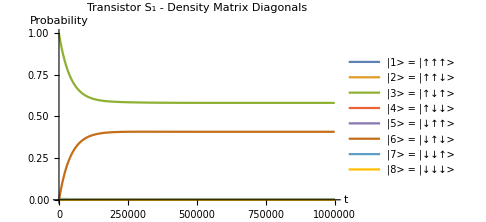
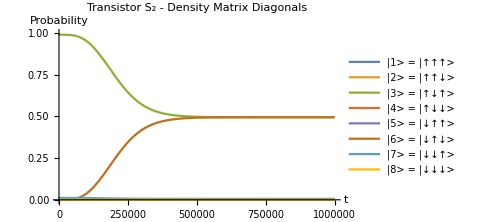

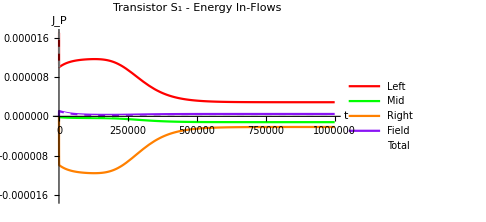
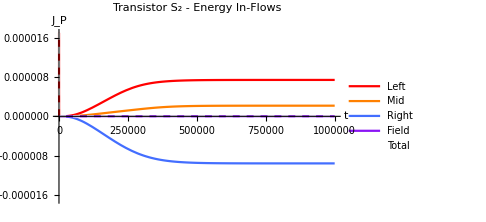

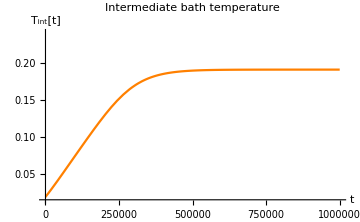

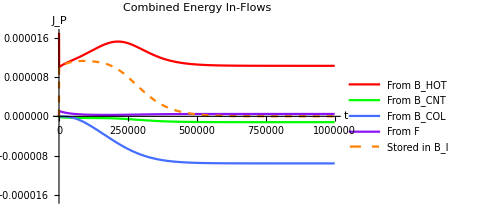

```mathematica
tmax=(10000/(Subscript[ωMR, 1] κhot))//.Flatten[{unitassum,sysassum}];

motioneqs=Simplify[{Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]];
initconditions={Tint[0]==Tcol,Table[Subscript[ρ, S,i,j][0]==i,j i,3 1,{S,1,2},{i,1,8},{j,1,8}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,8},{j,1,8}],Tint}],{t,0,tmax}
];

plot1=Flatten[{Table[Subscript[ρ, 1,i,i][t],{i,1,8}]}/.dynamics];
plot2=Flatten[{Table[Subscript[ρ, 2,i,i][t],{i,1,8}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S_1 - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}]}

plot1=Flatten[{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1],Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 1,2]+Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
plot2=Flatten[{
Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 2,2],Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 2],Subscript[EngyFlowIn, 2,1]+Subscript[EngyFlowIn, 2,2]+Subscript[EngyFlowIn, 2,3]+Subscript[EngyFlowInField, 2]
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Transistor S_1 - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv κhot/.sysassum,1.7 10^-3 Econv κhot/.sysassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Red,Green,Orange,PurpleC,{White,Dashed}}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Transistor S_2 - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv κhot/.sysassum,1.7 10^-3 Econv κhot/.sysassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Red,Orange,BlueC,PurpleC,{White,Dashed}}]}

Tint[t]/.dynamics;
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Intermediate bath temperature"],
	PlotRange-> {0.8Tcol/.sysassum,1.2Thot/.sysassum},
	AxesLabel->{Style["t"],Style["T_int[t]"]},
	PlotStyle->{Orange}
]

Flatten[{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2])
}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Combined Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv κhot/.sysassum,1.7 10^-3 Econv κhot/.sysassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"From B_HOT","From B_CNT","From B_COL","From F","Stored in B_I"},
	PlotStyle->{Red,Green,BlueC,PurpleC,{Orange,Dashed}}]
```

### Single transistor system, for comparison

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
indsysassum={
Subscript[T, 1,1]-> 0.2 Tconv,Subscript[T, 1,2]-> 0.02 Tconv,Subscript[T, 1,3]-> 0.02 Tconv,
Subscript[κ, 1,1]-> 0.01,Subscript[κ, 1,2]->0.01,Subscript[κ, 1,3]-> 0.01,
Subscript[ωL, 1]->0 ωconv,Subscript[ωM, 1]->0.0 ωconv,Subscript[ωR, 1]->0 ωconv,Subscript[ωLM, 1]-> 0.9ωconv,Subscript[ωMR, 1]->1.1 ωconv,Subscript[ωRL, 1]->0ωconv,
Subscript[Ω, 1]->0.007 ωconv
};
```

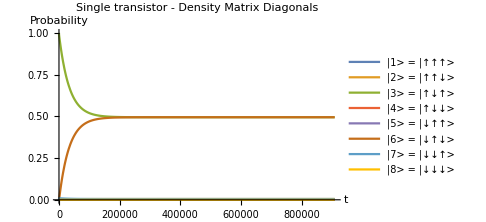

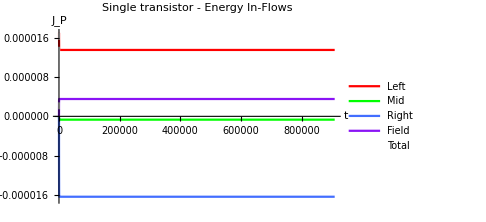

```mathematica
tmax=(10000/(Subscript[ωMR, 1] Subscript[κ, 1,1]))//.Flatten[{unitassum,indsysassum}];

motioneqs=Simplify[Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum}]];
initconditions={Table[Subscript[ρ, 1,i,j][0]==i,j i,3 1,{i,1,8},{j,1,8}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,8},{j,1,8}]}],{t,0,tmax}
];

Flatten[{Table[Subscript[ρ, 1,i,i][t],{i,1,8}]}/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Single transistor - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}]

Flatten[{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1],Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 1,2]+Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Single transistor - Energy In-Flows"],
	PlotRange->{Automatic, {-1.7 10^-3 Econv Subscript[κ, 1,1]/.indsysassum,1.7 10^-3 Econv Subscript[κ, 1,1]/.indsysassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Mid","Right","Field","Total"},
	PlotStyle->{Red,Green,BlueC,PurpleC,{White,Dashed}}]
```

## Density matrix, transition rate and energy flow at equilibrium

### Simulation of individual components at steady state

Function for density matrix elements, transition rates and energy flows,

```mathematica
Subscript[varFunc, S_][T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,Ωs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,ωassum,NBEassum,unitassum,Subscript[κ, S,1]-> κ1,Subscript[κ, S,2]-> κ2,Subscript[κ, S,3]-> κ3,Subscript[Ω, S]->Ωs,Subscript[T, S,1]-> T1,Subscript[T, S,2]-> T2,Subscript[T, S,3]-> T3,Subscript[ωL, S]->ωLs,Subscript[ωM, S]->ωMs,Subscript[ωR, S]->ωRs,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->ωRLs}];
temp1=N[Subscript[motioneq, S]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, S,i_,j_]'[t]-> 0,Subscript[ρ, S,i_,j_][t]-> Subscript[ρ, S,i,j]},1==∑_(i=1)^8 Subscript[ρ, S,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, S,i,j],{i,1,8},{j,1,8}]]]]];
Re[{Flatten[
Table[Subscript[ρ, S,i,i],{i,1,8}]/.temp3],
Flatten[{
Subscript[Τs, S,1][5,1],Subscript[Τs, S,1][6,2],Subscript[Τs, S,1][7,3],Subscript[Τs, S,1][8,4],
Subscript[Τs, S,2][3,1],Subscript[Τs, S,2][4,2],Subscript[Τs, S,2][7,5],Subscript[Τs, S,2][8,6],
Subscript[Τs, S,3][2,1],Subscript[Τs, S,3][4,3],Subscript[Τs, S,3][6,5],Subscript[Τs, S,3][8,7],
Subscript[Υs, S][3,1],Subscript[Υs, S][4,2],Subscript[Υs, S][7,5],Subscript[Υs, S][8,6]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],temp0}]/.temp3],
Flatten[{
Subscript[EngyFlowIn, S,1],Subscript[EngyFlowIn, S,2],Subscript[EngyFlowIn, S,3],Subscript[EngyFlowInField, S]
}//.Flatten[{Subscript[ρ, S,i_,j_][t]->Subscript[ρ, S,i,j],ωassum1,temp0}]/.temp3]}]
]
```

Function for drawing a state flow diagram,

```mathematica
DrawFlowGraph[label_,posx_,posy_,nodes_,rates_,ratecolors_,ratesF_,ratecolorsF_,title_,maxrate_]:=Module[{pos,psize},
psize=Dimensions[label][[1]];
pos[i_]:={posx[[i]],posy[[i]]};
Graphics[Flatten[{
{Thickness[0.0001],Arrowheads[0.06],Black,Arrow[{{1.15Min[posx],1.2Min[posy]},{1.15Min[posx],1.1Max[posy]}}]},Black,{Text[Style["Energy",FontSize->19.6,FontFamily->"Times New Roman"],{1.0Min[posx]+0.03,1.17Max[posy]}],Text[Style[title,FontSize->19.6,FontFamily->"Times New Roman"],{0,1.27Min[posy]}]},

Table[{Opacity[1],Thick,RGBColor[0.55,0.55,0.55],Disk[pos[i],0.01+0.25 √nodes[[i]]]},{i,1,psize}],
Table[
	If[rates[[i,j]]≠0 ,
		If[ ratesF[[i,j]]≠0,
			If[Abs[rates[[i,j]]]>Abs[ratesF[[i,j]]],
				{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			,
				{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			]
		,
			{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
			ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		]
	,
		If[ ratesF[[i,j]]≠0,
			{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
			ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		, Nothing]
	]
,{i,1,psize-1},{j,i+1,psize}],
Table[{Opacity[1],Black,Text[Style[label[[i]],FontSize->16],{posx[[i]]+{0.03,0.04,0.03,0.02,0.04,-0.00,0.07,-0.01}[[i]],posy[[i]]+{0.05,0.09,-0.06,-0.10,0.06,-0.06,-0.12,0.05}[[i]]}]},{i,1,psize}]

}], ImageSize->Medium]
]

DrawFunc[S_,ωLs_,ωMs_,ωRs_,ωLMs_,ωMRs_,ωRLs_,title_,colors_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF},temp0=Flatten[{ωassum1,Subscript[ωL, S]->ωLs,Subscript[ωM, S]->ωMs,Subscript[ωR, S]->ωRs,Subscript[ωLM, S]->ωLMs,Subscript[ωMR, S]->ωMRs,Subscript[ωRL, S]->ωRLs}];label={"|↑↑↑>","|↑↑↓>","|↑↓↑>","|↑↓↓>","|↓↑↑>","|↓↑↓>","|↓↓↑>","|↓↓↓>"};posx={0.15,-0.4,0.15,0.45,0.6,-0.15,-0.6,-0.15};posy=Table[Subscript[ω, S,i]/ωconv,{i,1,8}]//.temp0;nodes=var[[1]];rates=({{0, -var[[2]][[9]], -var[[2]][[5]], 0, -var[[2]][[1]], 0, 0, 0}, {0, 0, 0, -var[[2]][[6]], 0, -var[[2]][[2]], 0, 0}, {0, 0, 0, -var[[2]][[10]], 0, 0, -var[[2]][[3]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[4]]}, {0, 0, 0, 0, 0, -var[[2]][[11]], -var[[2]][[7]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[8]]}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[12]]}, {0, 0, 0, 0, 0, 0, 0, 0}});
ratesF=({{0, 0, -var[[2]][[13]], 0, 0, 0, 0, 0}, {0, 0, 0, -var[[2]][[14]], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -var[[2]][[15]], 0}, {0, 0, 0, 0, 0, 0, 0, -var[[2]][[16]]}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});ratecolors=({{0, colors[[3]], colors[[2]], 0, colors[[1]], 0, 0, 0}, {0, 0, 0, colors[[2]], 0, colors[[1]], 0, 0}, {0, 0, 0, colors[[3]], 0, 0, colors[[1]], 0}, {0, 0, 0, 0, 0, 0, 0, colors[[1]]}, {0, 0, 0, 0, 0, colors[[3]], colors[[2]], 0}, {0, 0, 0, 0, 0, 0, 0, colors[[2]]}, {0, 0, 0, 0, 0, 0, 0, colors[[3]]}, {0, 0, 0, 0, 0, 0, 0, 0}});
ratecolorsF=({{0, 0, colors[[4]], 0, 0, 0, 0, 0}, {0, 0, 0, colors[[4]], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, colors[[4]], 0}, {0, 0, 0, 0, 0, 0, 0, colors[[4]]}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Simulation for SI units

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=0.100/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Simulation for natural units

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

#### Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues of individual transistors, assuming T_INT is artificially fixed

For temperature-controlled Darlington pair,

```mathematica
Manipulate[Module[{tempS1,tempS2},
tempS1=Subscript[varFunc, 1][Thot,Tcnt,Tint,κhot,κcnt,κint,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,unitassum];
tempS2=Subscript[varFunc, 2][Thot,Tint,Tcol,κhot,κint,κcol,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum];
{
DrawFunc[1,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,StringForm["Transistor S_1"],{Red,Green,Orange,PurpleC},Τmax,tempS1],
DrawFunc[2,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,StringForm["Transistor S_2"],{Red,Orange,BlueC,PurpleC},Τmax,tempS2],
BarChart[tempS1[[3]]
,ChartLabels->{"S_1 - Left ","S_1 - Mid","S_1 - Right","S_1 - Field"},PlotLabel->"Transistor S_1 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax1,Emax1},ChartStyle->{Red,Green,Orange,PurpleC}],
BarChart[tempS2[[3]]
,ChartLabels->{"S_2 - Left ","S_2 - Mid","S_2 - Right","S_2 - Field"},PlotLabel->"Transistor S_2 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax2,Emax2},ChartStyle->{Red,Orange,BlueC,PurpleC}],
BarChart[{ -tempS1[[3,3]],-tempS2[[3,2]],-tempS1[[3,3]]-tempS2[[3,2]]}
,ChartLabels->{"S_1 - Right","S_2 - Mid","Total inflow"},PlotLabel->"Energy inflows to intermediate bath",AxesLabel->{"","J_P"},AxesOrigin->{0,0},ImageSize->Medium,PlotRange->{-Emaxint,Emaxint},ChartStyle->{Yellow,Brown,White}]
}
],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{Thot,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcnt,0.08 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcol,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Intermediate Bath Temperature",Alignment->Center],
{{Tint,0.14 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κhot,0.01},0.001,0.2},
{{κcnt,0.01},0.001,0.2},
{{κint,0.01},0.001,0.2},
{{κcol,0.01},0.001,0.2},
Delimiter,Item["Transistor S_1 - Parameters",Alignment->Center],
{{ωL1,0.0ωconv},0ωconv,2ωconv},
{{ωM1,0.0ωconv},0ωconv,2ωconv},
{{ωR1,0.0ωconv},0ωconv,2ωconv},
{{ωLM1,0.9ωconv},0ωconv,2ωconv},
{{ωMR1,1.1ωconv},0ωconv,2ωconv},
{{ωRL1,0.0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_1 - Optical Field",Alignment->Center],
{{Ω1,0.0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Transistor S_2 - Parameters",Alignment->Center],
{{ωL2,0.0ωconv},0ωconv,2ωconv},
{{ωM2,0.0ωconv},0ωconv,2ωconv},
{{ωR2,0.0ωconv},0ωconv,2ωconv},
{{ωLM2,0.9ωconv},0ωconv,2ωconv},
{{ωMR2,1.1ωconv},0ωconv,2ωconv},
{{ωRL2,0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_2 - Optical Field",Alignment->Center],
{{Ω2,0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax1,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Emax2,0.000014Econv},0.0000001Econv,0.00002Econv},
{{Emaxint,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Τmax,0.00006Τconv},0.000001Τconv,0.0002Τconv}]
```

For optically-controlled Darlington pair

```mathematica
Manipulate[Module[{tempS1,tempS2},
tempS1=Subscript[varFunc, 1][Thot,Tcnt,Tint,κhot,κcnt,κint,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,unitassum];
tempS2=Subscript[varFunc, 2][Thot,Tint,Tcol,κhot,κint,κcol,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum];
{
DrawFunc[1,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,StringForm["Transistor S_1"],{Red,Green,Orange,PurpleC},Τmax,tempS1],
DrawFunc[2,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,StringForm["Transistor S_2"],{Red,Orange,BlueC,PurpleC},Τmax,tempS2],
BarChart[tempS1[[3]]
,ChartLabels->{"S_1 - Left ","S_1 - Mid","S_1 - Right","S_1 - Field"},PlotLabel->"Transistor S_1 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax1,Emax1},ChartStyle->{Red,Green,Orange,PurpleC}],
BarChart[tempS2[[3]]
,ChartLabels->{"S_2 - Left ","S_2 - Mid","S_2 - Right","S_2 - Field"},PlotLabel->"Transistor S_2 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax2,Emax2},ChartStyle->{Red,Orange,BlueC,PurpleC}],
BarChart[{ -tempS1[[3,3]],-tempS2[[3,2]],-tempS1[[3,3]]-tempS2[[3,2]]}
,ChartLabels->{"S_1 - Right","S_2 - Mid","Total inflow"},PlotLabel->"Energy inflows to intermediate bath",AxesLabel->{"","J_P"},AxesOrigin->{0,0},ImageSize->Medium,PlotRange->{-Emaxint,Emaxint},ChartStyle->{Yellow,Brown,White}]
}
],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{Thot,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcnt,0.02 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcol,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Intermediate Bath Temperature",Alignment->Center],
{{Tint,0.175 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κhot,0.01},0.001,0.2},
{{κcnt,0.01},0.001,0.2},
{{κint,0.01},0.001,0.2},
{{κcol,0.01},0.001,0.2},
Delimiter,Item["Transistor S_1 - Parameters",Alignment->Center],
{{ωL1,0.0ωconv},0ωconv,2ωconv},
{{ωM1,0.1ωconv},0ωconv,2ωconv},
{{ωR1,0.0ωconv},0ωconv,2ωconv},
{{ωLM1,1.0ωconv},0ωconv,2ωconv},
{{ωMR1,1.0ωconv},0ωconv,2ωconv},
{{ωRL1,0.0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_1 - Optical Field",Alignment->Center],
{{Ω1,0.003ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Transistor S_2 - Parameters",Alignment->Center],
{{ωL2,0.0ωconv},0ωconv,2ωconv},
{{ωM2,0.0ωconv},0ωconv,2ωconv},
{{ωR2,0.0ωconv},0ωconv,2ωconv},
{{ωLM2,0.9ωconv},0ωconv,2ωconv},
{{ωMR2,1.1ωconv},0ωconv,2ωconv},
{{ωRL2,0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_2 - Optical Field",Alignment->Center],
{{Ω2,0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax1,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Emax2,0.000014Econv},0.0000001Econv,0.00002Econv},
{{Emaxint,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Τmax,0.00006Τconv},0.000001Τconv,0.0002Τconv}]
```

### Simulation of combined system at steady state

#### Finding the stable solution for a given configuration

Simulation for natural units. Required because FindRoot algorithm seems to get a lot of numerical errors when very small numbers are used

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

```mathematica
sysassum1:={
Subscript[ωL, 1]->0 ωconv,Subscript[ωM, 1]->0 ωconv,Subscript[ωR, 1]->0 ωconv,Subscript[ωLM, 1]->0.9 ωconv,Subscript[ωMR, 1]->1.1 ωconv,Subscript[ωRL, 1]->0ωconv,
Subscript[ωL, 2]->0 ωconv,Subscript[ωM, 2]->0 ωconv,Subscript[ωR, 2]->0 ωconv,Subscript[ωLM, 2]->0.9 ωconv,Subscript[ωMR, 2]->1.1ωconv,Subscript[ωRL, 2]->0ωconv,
Subscript[Ω, 1]->0.0ωconv,Subscript[Ω, 2]->0ωconv,
Thot-> 0.2 Tconv,Tcol-> 0.02 Tconv,Tcnt-> 0.04 Tconv,
κhot->0.01,κcol->0.01,κcnt->0.01,κint->0.01
};
```

Conditions for the steady state solutions. The time derivatives have all become zero.

```mathematica
statassum=Flatten[{
Tint'[t]->0,
Tint[t]->Tint,
Table[Subscript[ρ, S,i,j]'[t]->0,{S,1,2},{i,1,8},{j,1,8}],
Table[Subscript[ρ, S,i,j][t]->Subscript[ρ, S,i,j],{S,1,2},{i,1,8},{j,1,8}]
}];
```

Conditions for the density matrices to be valid.

```mathematica
Subscript[denmateq, S_]:=∑_(i=1)^8 Subscript[ρ, S,i,i]==1
```

The equations of motion consists of
	2×56 off diagonal equations, 
	2×7 diagonal equations (one is removed since not all 8 equations are independent of each other), 
	2 density matrix trace equations, 
	1 equation for the intermediate bath

```mathematica
stateqns=Expand[Flatten[{
Subscript[motioneqoffdiag, 1],Subscript[motioneqoffdiag, 2],
Subscript[motioneqdiag, 1][[1;;7]],Subscript[motioneqdiag, 2][[1;;7]],
Subscript[denmateq, 1],Subscript[denmateq, 2],
motioneqintbath}]];
```

Generate a random point starting point for the equation solver

```mathematica
startpoints:=Module[{temp},
temp=Flatten[Table[{Subscript[ρ, S,i,j],RandomReal[{0,1}]},{S,1,2},{i,1,8},{j,1,8}],2];
AppendTo[temp,{Tint,RandomReal[{Tcol/.sysassum1,Thot/.sysassum1}]}]
];
```

Run the solver. “Solve” doesn’t work since this is a complicated non-linear equation

```mathematica
statsol=FindRoot[stateqns//.Flatten[{statassum,unitassum,ωassum,ωassum1,sysassum1,Jassum,NBEassum,Tassum}],startpoints];
Tint/.statsol
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0610811

#### Combining above methodology into a single function

```mathematica
combinedVarFunc[Thots_,Tcnts_,Tcols_,κhots_,κcnts_,κints_,κcols_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,Ω1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,unitassum_]:=
Module[{temp0,temp1,temp2},
temp0=Flatten[{statassum,unitassum,Jassum,NBEassum,ωassum,ωassum1,Tassum,
Thot->Thots,Tcnt->Tcnts,Tcol->Tcols,
κhot->κhots,κcnt->κcnts,κint->κints,κcol->κcols,
Subscript[ωL, 1]->ωL1,Subscript[ωM, 1]->ωM1,Subscript[ωR, 1]->ωR1,Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[ωRL, 1]->ωRL1,Subscript[Ω, 1]->Ω1,
Subscript[ωL, 2]->ωL2,Subscript[ωM, 2]->ωM2,Subscript[ωR, 2]->ωR2,Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,Subscript[ωRL, 2]->ωRL2,Subscript[Ω, 2]->Ω2}];

temp1=stateqns//.temp0;
temp2=FindRoot[temp1,startpoints];
Re[{Tint//.temp2,Table[{
	Table[Subscript[ρ, S,i,i],{i,1,8}]/.temp2,
	{
		Subscript[Τs, S,1][5,1],Subscript[Τs, S,1][6,2],Subscript[Τs, S,1][7,3],Subscript[Τs, S,1][8,4],
		Subscript[Τs, S,2][3,1],Subscript[Τs, S,2][4,2],Subscript[Τs, S,2][7,5],Subscript[Τs, S,2][8,6],
		Subscript[Τs, S,3][2,1],Subscript[Τs, S,3][4,3],Subscript[Τs, S,3][6,5],Subscript[Τs, S,3][8,7],
		Subscript[Υs, S][3,1],Subscript[Υs, S][4,2],Subscript[Υs, S][7,5],Subscript[Υs, S][8,6]
	}//.Flatten[{temp0,temp2}],
	{
		Subscript[EngyFlowIn, S,1],Subscript[EngyFlowIn, S,2],Subscript[EngyFlowIn, S,3],Subscript[EngyFlowInField, S]
	}//.Flatten[{temp0,temp2}]
},{S,1,2}]
}]
]
```

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2},
ωL1=0 ωconv;ωM1=0 ωconv;ωR1=0 ωconv;ωLM1=0.9 ωconv;ωMR1=1.1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0 ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω1=0.003ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;Tcnt= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum]
]
```

{0.162376,{{{3.26935×10^-6,0.00540817,0.493965,0.00062402,0.00062402,0.493965,0.00540817,3.26935×10^-6},{3.33363×10^-8,7.2156×10^-7,-7.2156×10^-7,-3.33363×10^-8,-6.5387×10^-8,1.24761×10^-6,-1.24761×10^-6,6.5387×10^-8,3.20507×10^-8,6.56172×10^-7,-6.56172×10^-7,-3.20507×10^-8,-3.643×10^-42,-1.93711×10^-6,1.93711×10^-6,2.18847×10^-42},{1.35881×10^-6,-7.60591×10^-7,-1.37307×10^-6,7.74846×10^-7}},{{1.8717×10^-6,0.00512673,0.494567,0.000304604,0.000304604,0.494567,0.00512673,1.8717×10^-6},{1.37621×10^-8,3.34382×10^-6,-3.34382×10^-6,-1.37621×10^-8,6.82657×10^-9,-3.3644×10^-6,3.3644×10^-6,-6.82657×10^-9,-2.05887×10^-8,3.35064×10^-6,-3.35064×10^-6,2.05887×10^-8,0,0,0,0},{6.04364×10^-6,1.37307×10^-6,-7.41671×10^-6,0}}}}

For temperature-controlled case

```mathematica
Manipulate[Module[{temp},
temp=combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum];
{
DrawFunc[1,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,StringForm["Transistor S_1"],{Red,Green,Orange,PurpleC},Τmax,temp[[2,1]]],
DrawFunc[2,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,StringForm["Transistor S_2"],{Red,Orange,BlueC,PurpleC},Τmax,temp[[2,2]]],
BarChart[temp[[2,1,3]]
,ChartLabels->{"S_1 - Left ","S_1 - Mid","S_1 - Right","S_1 - Field"},PlotLabel->"Transistor S_1 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax1,Emax1},ChartStyle->{Red,Green,Orange,PurpleC}],
BarChart[temp[[2,2,3]]
,ChartLabels->{"S_2 - Left ","S_2 - Mid","S_2 - Right","S_2 - Field"},PlotLabel->"Transistor S_2 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax2,Emax2},ChartStyle->{Red,Orange,BlueC,PurpleC}],
StringForm["Tint = ``",NumberForm[temp[[1]],4]]
}

],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{Thot,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcnt,0.08 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcol,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κhot,0.01},0.001,0.2},
{{κcnt,0.01},0.001,0.2},
{{κint,0.01},0.001,0.2},
{{κcol,0.01},0.001,0.2},
Delimiter,Item["Transistor S_1 - Parameters",Alignment->Center],
{{ωL1,0.0ωconv},0ωconv,2ωconv},
{{ωM1,0.0ωconv},0ωconv,2ωconv},
{{ωR1,0.0ωconv},0ωconv,2ωconv},
{{ωLM1,0.9ωconv},0ωconv,2ωconv},
{{ωMR1,1.1ωconv},0ωconv,2ωconv},
{{ωRL1,0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_1 - Optical Field",Alignment->Center],
{{Ω1,0.0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Transistor S_2 - Parameters",Alignment->Center],
{{ωL2,0.0ωconv},0ωconv,2ωconv},
{{ωM2,0.0ωconv},0ωconv,2ωconv},
{{ωR2,0.0ωconv},0ωconv,2ωconv},
{{ωLM2,0.9ωconv},0ωconv,2ωconv},
{{ωMR2,1.1ωconv},0ωconv,2ωconv},
{{ωRL2,0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_2 - Optical Field",Alignment->Center],
{{Ω2,0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax1,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Emax2,0.000014Econv},0.0000001Econv,0.00002Econv},
{{Emaxint,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Τmax,0.00006Τconv},0.000001Τconv,0.0002Τconv},
ContinuousAction->False]
```

For optically-controlled case

```mathematica
Manipulate[Module[{temp},
temp=combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum];
{
StringForm["Tint = ``",NumberForm[temp[[1]],4]],
DrawFunc[1,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,StringForm["Transistor S_1"],{Red,Green,Orange,PurpleC},Τmax,temp[[2,1]]],
DrawFunc[2,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,StringForm["Transistor S_2"],{Red,Orange,BlueC,PurpleC},Τmax,temp[[2,2]]],
BarChart[temp[[2,1,3]]
,ChartLabels->{"S_1 - Left ","S_1 - Mid","S_1 - Right","S_1 - Field"},PlotLabel->"Transistor S_1 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax1,Emax1},ChartStyle->{Red,Green,Orange,PurpleC}],
BarChart[temp[[2,2,3]]
,ChartLabels->{"S_2 - Left ","S_2 - Mid","S_2 - Right","S_2 - Field"},PlotLabel->"Transistor S_2 Energy inflows",AxesLabel->{"","J_P"},ImageSize->Medium,PlotRange->{-Emax2,Emax2},ChartStyle->{Red,Orange,BlueC,PurpleC}]
}

],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{Thot,0.20 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcnt,0.02 Tconv},0.01 Tconv,0.22 Tconv},
{{Tcol,0.02 Tconv},0.01 Tconv,0.22 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κhot,0.01},0.001,0.2},
{{κcnt,0.01},0.001,0.2},
{{κint,0.01},0.001,0.2},
{{κcol,0.01},0.001,0.2},
Delimiter,Item["Transistor S_1 - Parameters",Alignment->Center],
{{ωL1,0.0ωconv},0ωconv,2ωconv},
{{ωM1,0.1ωconv},0ωconv,2ωconv},
{{ωR1,0.0ωconv},0ωconv,2ωconv},
{{ωLM1,1ωconv},0ωconv,2ωconv},
{{ωMR1,1ωconv},0ωconv,2ωconv},
{{ωRL1,0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_1 - Optical Field",Alignment->Center],
{{Ω1,0.003ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Transistor S_2 - Parameters",Alignment->Center],
{{ωL2,0.0ωconv},0ωconv,2ωconv},
{{ωM2,0.0ωconv},0ωconv,2ωconv},
{{ωR2,0.0ωconv},0ωconv,2ωconv},
{{ωLM2,0.9ωconv},0ωconv,2ωconv},
{{ωMR2,1.1ωconv},0ωconv,2ωconv},
{{ωRL2,0ωconv},0ωconv,2ωconv},
Delimiter,Item["Transistor S_2 - Optical Field",Alignment->Center],
{{Ω2,0ωconv},0ωconv,0.01ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax1,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Emax2,0.000014Econv},0.0000001Econv,0.00002Econv},
{{Emaxint,0.000004Econv},0.0000001Econv,0.00002Econv},
{{Τmax,0.00006Τconv},0.000001Τconv,0.0002Τconv},
ContinuousAction->False]
```

## Plots for total thermal flow through B_INT

Simulation for SI units

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Simulation for natural units

```mathematica
unitassum = {k-> 1,ℏ->1};
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Energy flows through B_INT for different temperatures T_INT, while keeping Ω and T_CNT constant. To prove only a single stationary point exists within the practical temperature range

```mathematica
PlotEngyFlowsOfBintWRTTint[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,Ω1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Tintmin_,Tintmax_,Tres_,legends_]:=Module[{tempx,tempyS1,tempyS2,tempy,Bintflows},
tempx=Table[{Tint,Tint,Tint},{Tint,Tintmin,Tintmax,Tres}];
tempyS1=Table[Subscript[varFunc, 1][Thot,Tcnt,Tint,κhot,κcnt,κint,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,unitassum],{Tint,Tintmin,Tintmax,Tres}];
tempyS2=Table[Subscript[varFunc, 2][Thot,Tint,Tcol,κhot,κint,κcol,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Tint,Tintmin,Tintmax,Tres}];
tempy=10^11 MapThread[List,{-tempyS1[[;;,3,3]],tempyS2[[;;,3,2]],(-tempyS1[[;;,3,3]]-tempyS2[[;;,3,2]])}];
Bintflows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,3}];

ListPlot[Bintflows,
	ImageSize->Medium,
	PlotRange->{{Tintmin,Tintmax},Automatic},
	AxesLabel->{
		Style[" T_I(K)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	AxesStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	PlotLegends->legends &&{
		Style["J_I1",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_I2",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_I1-J_I2",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0.5,0],Dashed},{RGBColor[1,0.5,0],DotDashed},{RGBColor[1,0.5,0]}},
	Joined->True]
]
```

```mathematica
PlotEngyFlowsOfBintWRTTint[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,Ω1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Tintmin_,Tintmax_,Tres_,legends_]:=Module[{tempx,tempyS1,tempyS2,tempy,Bintflows},
tempx=Table[{Tint,Tint,Tint},{Tint,Tintmin,Tintmax,Tres}];
tempyS1=Table[Subscript[varFunc, 1][Thot,Tcnt,Tint,κhot,κcnt,κint,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,unitassum],{Tint,Tintmin,Tintmax,Tres}];
tempyS2=Table[Subscript[varFunc, 2][Thot,Tint,Tcol,κhot,κint,κcol,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Tint,Tintmin,Tintmax,Tres}];
tempy=MapThread[List,{-tempyS1[[;;,3,3]],tempyS2[[;;,3,2]],(-tempyS1[[;;,3,3]]-tempyS2[[;;,3,2]])}];
Bintflows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,i]]}],{i,1,3}];

ListPlot[Bintflows,
	ImageSize->Medium,
	PlotLabel->"Intermediate bath thermal flows",
	PlotRange->{{Tintmin,Tintmax},Automatic},
	AxesLabel->{Style["T_int"],Style["J_P"]},
	PlotLegends->legends &&{"J_I1","J_I2","J_I1-J_I2"},
	PlotStyle->{{RGBColor[1,0.5,0],Dashed},{RGBColor[1,0.5,0],DotDashed},{RGBColor[1,0.5,0]}},
	Joined->True]
]
```

Under a temperature-controlled configuration

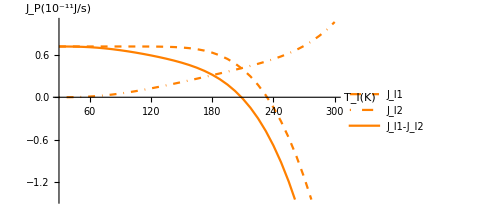

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tintmin,Tintmax,Tres},
ωL1=0 ωconv;ωM1=0 ωconv;ωR1=0 ωconv;ωLM1=0.9 ωconv;ωMR1=1.1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0 ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.08 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
Tintmin=Tcol;Tintmax=Thot;Tres=0.005Tconv;
PlotEngyFlowsOfBintWRTTint[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tintmin,Tintmax,Tres,True]
]
```

Under an optically-controlled configuration

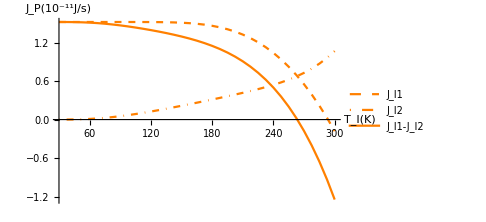

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tintmin,Tintmax,Tres},
ωL1=0 ωconv;ωM1=0.1ωconv;ωR1=0 ωconv;ωLM1=1 ωconv;ωMR1=1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0 ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω1=0.003ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
Tintmin=Tcol;Tintmax=Thot;Tres=0.005Tconv;
PlotEngyFlowsOfBintWRTTint[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tintmin,Tintmax,Tres,True]
]
```

## Plots for adjusting T_CNT while keeping Ω constant (operation as a thermal transistor)

### Absolute thermal flows

Generate a fixed starting point for the equation solver

```mathematica
startpoints:=Module[{temp},
temp=Flatten[Table[{Subscript[ρ, S,i,j],i,3 j,3 1},{S,1,2},{i,1,8},{j,1,8}],2];
AppendTo[temp,{Tint,Thot/.sysassum1}]
];
```

Inwards energy flows when temperature T_CNT is changed, keeping Ω constant,

```mathematica
PlotEngyFlowsWithTcnt[Thot_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,Ω1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Tcntmin_,Tcntmax_,Tres_,legends_]:=Module[{tempx,tempy,tran1flows,tran2flows,inttemps,combflows},
tempx=Table[{Tcnt,Tcnt,Tcnt},{Tcnt,Tcntmin,Tcntmax,Tres}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
tran1flows=Table[MapThread[List,{tempx[[;;,i]],10^12 tempy[[;;,2,1,3,i]]}],{i,1,3}];
tran2flows=Table[MapThread[List,{tempx[[;;,i]],10^11 tempy[[;;,2,2,3,i]]}],{i,1,3}];
inttemps=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,1]]}],{i,1,1}];
combflows={
	MapThread[List,{tempx[[;;,1]],10^11(tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]])}],
	MapThread[List,{tempx[[;;,2]],10^11 tempy[[;;,2,1,3,2]]}],
	MapThread[List,{tempx[[;;,3]],10^11 tempy[[;;,2,2,3,3]]}]
};
{
ListPlot[inttemps,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},{Tcol,Thot}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->15],
		Style["T_I(K)",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	PlotStyle->{RGBColor[1,0.5,0]},
	Joined->True],
ListPlot[combflows,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["-J_C",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]},{RGBColor[0.2627,0.4313,1]}},
	Joined->True],
ListPlot[tran1flows,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-12J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_L^S_1",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_M^S_1",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_R^S_1",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[1,0.5,0],Dashed}},
	Joined->True],
ListPlot[tran2flows,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_L^S_2",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_M^S_2",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_R^S_2",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[1,0.5,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed}},
	Joined->True]
}]
```

```mathematica
PlotEngyFlowsWithTcnt[Thot_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,Ω1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Tcntmin_,Tcntmax_,Tres_,legends_]:=Module[{tempx,tempy,tran1flows,tran2flows,inttemps,combflows},
tempx=Table[{Tcnt,Tcnt,Tcnt},{Tcnt,Tcntmin,Tcntmax,Tres}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
tran1flows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,1,3,i]]}],{i,1,3}];
tran2flows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,2,3,i]]}],{i,1,3}];
inttemps=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,1]]}],{i,1,1}];
combflows={
	MapThread[List,{tempx[[;;,1]],tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]]}],
	MapThread[List,{tempx[[;;,2]],tempy[[;;,2,1,3,2]]}],
	MapThread[List,{tempx[[;;,3]],tempy[[;;,2,2,3,3]]}]
};
{
ListPlot[inttemps,
	ImageSize->Medium,
	PlotLabel->"Intermediate bath temperature",
	PlotRange->{{Tcntmin,Tcntmax},{Tcol,Thot}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["T_N"],Style["T_I"]},
	PlotStyle->{RGBColor[1,0.5,0]},
	Joined->True],
ListPlot[combflows,
	ImageSize->Medium,
	PlotLabel->"Combined system - Heat flows",
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["T_N"],Style["J_P"]},
	GridLines->{None,{0}},
	PlotLegends->legends &&{Style["J_H"],Style["J_N"],Style["-J_C"]},
	PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]},{RGBColor[0.2627,0.4313,1]}},	
	Joined->True],
ListPlot[tran1flows,
	ImageSize->Medium,
	PlotLabel->"Transistor 1 - Heat flows",
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["T_N"],Style["J_P"]},
	GridLines->{None,{0}},
	PlotLegends->legends &&{Style["J_L^S_1"],Style["J_M^S_1"],Style["J_R^S_1"]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[1,0.5,0],Dashed}},
	Joined->True],
ListPlot[tran2flows,
	ImageSize->Medium,
	PlotLabel->"Transistor 2 - Heat flows",
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["T_N"],Style["J_P"]},
	GridLines->{None,{0}},
	PlotLegends->legends &&{Style["J_L^S_2"],Style["J_M^S_2"],Style["J_R^S_2"]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[1,0.5,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed}},
	Joined->True]
}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 28. digits of working precision to meet these tolerances.

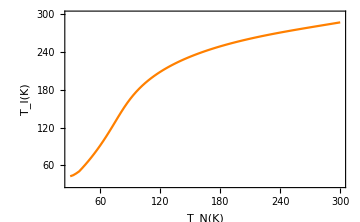
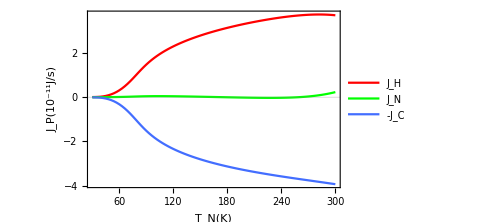
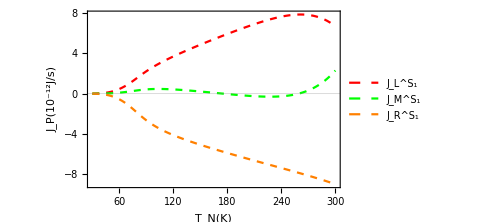
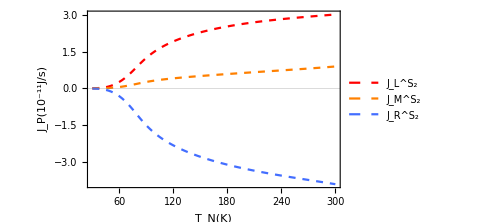

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tcntmin,Tcntmax,Tres},
ωL1=0 ωconv;ωM1=0 ωconv;ωR1=0 ωconv;ωLM1=0.9 ωconv;ωMR1=1.1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0 ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tcntmin,Tcntmax,Tres,True]
]
combFlowGraph1=%[[2]];
```

For comparison, a single temperature-controlled quantum thermal transistor

```mathematica
PlotEngyFlowsWithTcntSingle[Thot_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ω_,Tcntmin_,Tcntmax_,Tres_,legends_]:=Module[{tempx,tempy,singleflows},
tempx=Table[{Tcnt,Tcnt,Tcnt},{Tcnt,Tcntmin,Tcntmax,Tres}];
tempy=10^11 Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
singleflows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,3,i]]}],{i,1,3}];
ListPlot[singleflows,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["-J_C",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed}},
	Joined->True]
]
```

```mathematica
PlotEngyFlowsWithTcntSingle[Thot_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ω_,Tcntmin_,Tcntmax_,Tres_,legends_]:=Module[{tempx,tempy,singleflows},
tempx=Table[{Tcnt,Tcnt,Tcnt},{Tcnt,Tcntmin,Tcntmax,Tres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
singleflows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,3,i]]}],{i,1,3}];
ListPlot[singleflows,
	ImageSize->Medium,
	PlotLabel->"Single transistor - Heat flows",
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["T_N"],Style["J_P"]},
	GridLines->{None,{0}},
	PlotLegends->legends &&{Style["J_H"],Style["J_N"],Style["-J_C"]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed}},	
	Joined->True]
]
```

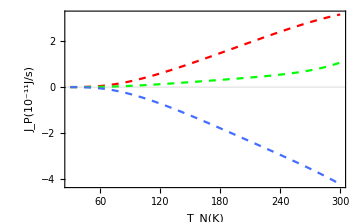

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,Tcntmin,Tcntmax,Tres},
ωL=0 ωconv;ωM=0 ωconv;ωR=0 ωconv;ωLM=0.9ωconv;ωMR=1.1 ωconv;ωRL=0ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,Tcntmin,Tcntmax,Tres,False]
]
singlFlowGraph1=%;
```

Plotting the two graphs on top of each other

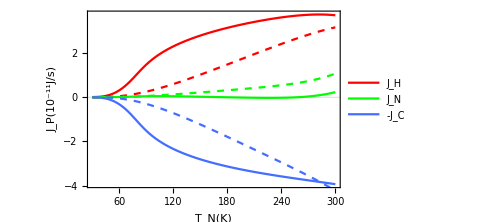

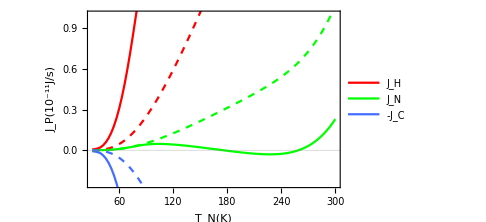

```mathematica
Show[combFlowGraph1,singlFlowGraph1]
Show[combFlowGraph1,singlFlowGraph1,PlotRange->{Full,{-0.25,1}}]
```

### Amplification factors

Amplification factor of the thermal transistor action is given by the ratio α_Te=ΔJ_H/ΔJ_N

```mathematica
PlotAmplificationWithTcnt[Thot_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,Ω1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Tcntmin_,Tcntmax_,Tres_]:=Module[{tempx,tempy,ampl,tempJH,tempJN,tempampl},
tempx=Table[Tcnt,{Tcnt,Tcntmin,Tcntmax-Tres,Tres}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
tempJH=tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]];
tempJN=tempy[[;;,2,1,3,2]];
tempampl=Differences[tempJH]/Differences[tempJN];
ampl=MapThread[List,{tempx,tempampl}];
ListPlot[ampl,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->15],
		Style["α_Te = ΔJ_H/ΔJ_N",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},	
	PlotStyle->{Black},
	Joined->True]
]
```

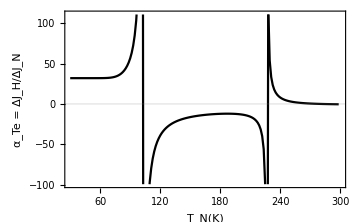

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tcntmin,Tcntmax,Tres},
ωL1=0 ωconv;ωM1=0 ωconv;ωR1=0 ωconv;ωLM1=0.9 ωconv;ωMR1=1.1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0 ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.1;κcol=0.1;κcnt=0.1;κint=0.1;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.001Tconv;
PlotAmplificationWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tcntmin,Tcntmax,Tres]
]
combAmplGraph1=%;
```

```mathematica
PlotAmplificationWithTcntSingle[Thot_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ω_,Tcntmin_,Tcntmax_,Tres_]:=Module[{tempx,tempy,tempJH,tempJN,tempampl,singleeffic},
tempx=Table[Tcnt,{Tcnt,Tcntmin,Tcntmax-Tres,Tres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
tempJH=tempy[[;;,3,1]];
tempJN=tempy[[;;,3,2]];
tempampl=Differences[tempJH]/Differences[tempJN];
singleeffic=MapThread[List,{tempx,tempampl}];
ListPlot[singleeffic,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},{0,5}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->15],
		Style["α_Te = ΔJ_H/ΔJ_N",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{{Black,Dashed}},
	Joined->True]
]
```

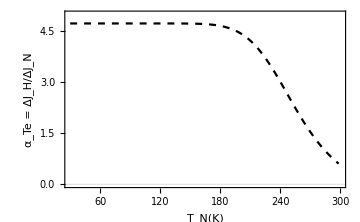

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,Tcntmin,Tcntmax,Tres},
ωL=0 ωconv;ωM=0 ωconv;ωR=0 ωconv;ωLM=0.9ωconv;ωMR=1.1 ωconv;ωRL=0ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.1;κcol=0.1;κcnt=0.1;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.001Tconv;
PlotAmplificationWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,Tcntmin,Tcntmax,Tres]
]
singlAmplGraph1=%;
```

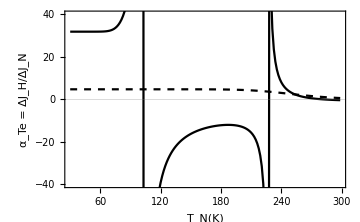

```mathematica
Show[combAmplGraph1,singlAmplGraph1,PlotRange->{Full,{-40,40}}]
```

### Thermal efficiency

Energy efficiency of the thermal transistor action is given by the ratio β_Te=J_H/J_N

```mathematica
PlotEngyEfficiencyWithTcnt[Thot_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,Ω1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Tcntmin_,Tcntmax_,Tres_]:=Module[{tempx,tempy,tempJH,tempJN,effic},
tempx=Table[Tcnt,{Tcnt,Tcntmin,Tcntmax,Tres}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
tempJH=tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]];
tempJN=tempy[[;;,2,1,3,2]];
effic=MapThread[List,{tempx,tempJH/tempJN}];
ListPlot[effic,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->15],
		Style["β_Te = J_H/J_N",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{Black},
	Joined->True]
]
```

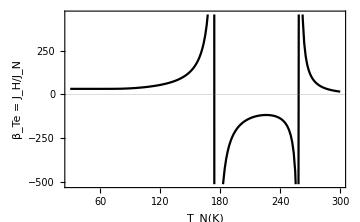

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tcntmin,Tcntmax,Tres},
ωL1=0 ωconv;ωM1=0 ωconv;ωR1=0 ωconv;ωLM1=0.9 ωconv;ωMR1=1.1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0 ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.1;κcol=0.1;κcnt=0.1;κint=0.1;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.001Tconv;
PlotEngyEfficiencyWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tcntmin,Tcntmax,Tres]
]
combEfficGraph1=%;
```

```mathematica
PlotEngyEfficiencyWithTcntSingle[Thot_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ω_,Tcntmin_,Tcntmax_,Tres_]:=Module[{tempx,tempy,tempJH,tempJN,singleeffic},
tempx=Table[Tcnt,{Tcnt,Tcntmin,Tcntmax,Tres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
tempJH=tempy[[;;,3,1]];
tempJN=tempy[[;;,3,2]];
singleeffic=MapThread[List,{tempx,tempJH/tempJN}];
ListPlot[singleeffic,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},{0,5}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->15],
		Style["β_Te = J_H/J_N",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{{Black,Dashed}},
	Joined->True]
]
```

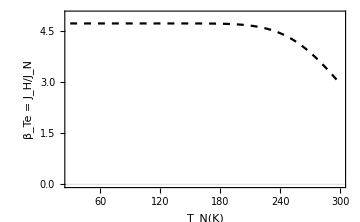

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,Tcntmin,Tcntmax,Tres},
ωL=0 ωconv;ωM=0 ωconv;ωR=0 ωconv;ωLM=0.9ωconv;ωMR=1.1 ωconv;ωRL=0ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.1;κcol=0.1;κcnt=0.1;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.001Tconv;
PlotEngyEfficiencyWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,Tcntmin,Tcntmax,Tres]
]
singlEfficGraph1=%;
```

Plotting the two graphs on top of each other

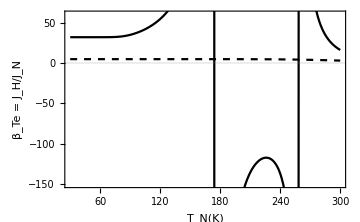

```mathematica
Show[combEfficGraph1,singlEfficGraph1,PlotRange->{Full,{-150,60}}]
```

### Sensitivity to the temperature

Sensitivity of the thermal transistor action to changes in the temperature is given by the ratio η_Te^P=ΔJ_P/ΔT_N

```mathematica
PlotSensitivityWithTcnt[Thot_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,Ω1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Tcntmin_,Tcntmax_,Tres_,legends_]:=Module[{tempx,tempy,tempJH,tempJN,tempJC,sensi},
tempx=Table[Tcnt,{Tcnt,Tcntmin,Tcntmax-Tres,Tres}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
tempJH=tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]];
tempJN=tempy[[;;,2,1,3,2]];
tempJC=tempy[[;;,2,2,3,3]];
sensi={
	MapThread[List,{tempx,10^13 1/Tres Differences[tempJH]}],
	MapThread[List,{tempx,10^13 1/Tres Differences[tempJN]}],
	MapThread[List,{tempx,10^13 1/Tres Differences[tempJC]}]
};
ListPlot[sensi,
	ImageSize->Medium,
	PlotRange->{{Tcntmin,Tcntmax},Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-13η_Te^P",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["η_Te^H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["η_Te^N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["-η_Te^C",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]},{RGBColor[0.2627,0.4313,1]}},
	Joined->True]
]
```

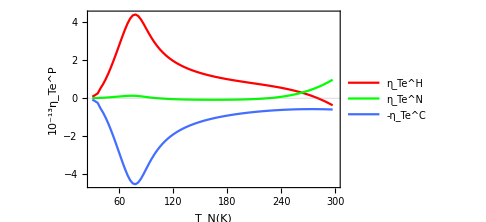

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tcntmin,Tcntmax,Tres},
ωL1=0 ωconv;ωM1=0 ωconv;ωR1=0 ωconv;ωLM1=0.9 ωconv;ωMR1=1.1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0 ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω1=0ωconv;Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotSensitivityWithTcnt[Thot,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Tcntmin,Tcntmax,Tres,True]
]
sensiGraph1=%;
```

```mathematica
PlotSensitivityWithTcntSingle[Thot_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ω_,Tcntmin_,Tcntmax_,Tres_,legends_]:=Module[{tempx,tempy,tempJH,tempJN,tempJC,singlesensi},
tempx=Table[Tcnt,{Tcnt,Tcntmin,Tcntmax-Tres,Tres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
tempJH=tempy[[;;,3,1]];
tempJN=tempy[[;;,3,2]];
tempJC=tempy[[;;,3,3]];
singlesensi={
	MapThread[List,{tempx,10^13 1/Tres Differences[tempJH]}],
	MapThread[List,{tempx,10^13 1/Tres Differences[tempJN]}],
	MapThread[List,{tempx,10^13 1/Tres Differences[tempJC]}]
};
ListPlot[singlesensi,
	ImageSize->Medium,
	PlotRange->{Full,Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N(K)",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-13η_P",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["η_Te^H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["η_Te^N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["-η_Te^C",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed}},
	Joined->True]
]
```

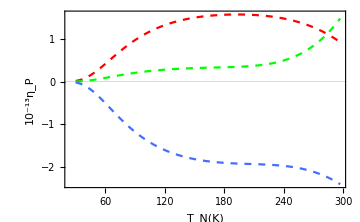

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,Tcntmin,Tcntmax,Tres},
ωL=0 ωconv;ωM=0 ωconv;ωR=0 ωconv;ωLM=0.9ωconv;ωMR=1.1 ωconv;ωRL=0ωconv;
Ω=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Tcntmin= 0.02 Tconv;Tcntmax=0.2 Tconv;Tres=0.002Tconv;
PlotSensitivityWithTcntSingle[Thot,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,Tcntmin,Tcntmax,Tres,False]
]
singlSensiGraph1=%;
```

Plotting the two graphs on top of each other

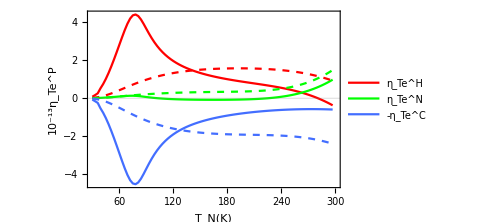

```mathematica
Show[sensiGraph1,singlSensiGraph1]
```

## Plots for adjusting Ω while keeping T_CNT constant (operation as an optically controlled thermal gate)

### Absolute thermal flows

Inwards energy flows when temperature Ω is changed, keeping T_CNT constant,

```mathematica
PlotEngyFlowsWithΩ[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Ω1min_,Ω1max_,Ω1res_,legends_]:=Module[{tempx,tempy,tran1flows,tran2flows,inttemps,combflows},
tempx=10^-10/(2π)Table[{Ω1,Ω1,Ω1,Ω1},{Ω1,Ω1min,Ω1max,Ω1res}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Ω1,Ω1min,Ω1max,Ω1res}];
tran1flows=Table[MapThread[List,{tempx[[;;,i]],10^10 tempy[[;;,2,1,3,i]]}],{i,1,4}];
tran2flows=Table[MapThread[List,{tempx[[;;,i]],10^9 tempy[[;;,2,2,3,i]]}],{i,1,3}];
inttemps=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,1]]}],{i,1,1}];
combflows={
	MapThread[List,{tempx[[;;,1]],10^11(tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]])}],
	MapThread[List,{tempx[[;;,2]],10^11 tempy[[;;,2,1,3,2]]}],
	MapThread[List,{tempx[[;;,3]],10^11 tempy[[;;,2,2,3,3]]}],
	MapThread[List,{tempx[[;;,4]],10^11 tempy[[;;,2,1,3,4]]}]
};
{
ListPlot[inttemps,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ω1min,Ω1max},{Tcol,Thot}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->15],
		Style["T_I(K)",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	PlotStyle->{RGBColor[1,0.5,0]},
	Joined->True],
ListPlot[combflows,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ω1min,Ω1max},Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["-J_C",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_F",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]},{RGBColor[0.2627,0.4313,1]},{RGBColor[0.5411,0.0784,0.9607]}},
	Joined->True],
ListPlot[tran1flows,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ω1min,Ω1max},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-12J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_L^S_1",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_M^S_1",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_R^S_1",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_F^S_1",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[1,0.5,0],Dashed},{RGBColor[0.5411,0.0784,0.9607],Dashed}},
	Joined->True],
ListPlot[tran2flows,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ω1min,Ω1max},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_L^S_2",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_M^S_2",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_R^S_2",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[1,0.5,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed}},
	Joined->True]
}]
```

```mathematica
PlotEngyFlowsWithΩ[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Ω1min_,Ω1max_,Ω1res_,legends_]:=Module[{tempx,tempy,tran1flows,tran2flows,inttemps,combflows},
tempx=Table[{Ω1,Ω1,Ω1,Ω1},{Ω1,Ω1min,Ω1max,Ω1res}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Ω1,Ω1min,Ω1max,Ω1res}];
tran1flows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,1,3,i]]}],{i,1,4}];
tran2flows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,2,2,3,i]]}],{i,1,3}];
inttemps=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,1]]}],{i,1,1}];
combflows={
	MapThread[List,{tempx[[;;,1]],tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]]}],
	MapThread[List,{tempx[[;;,2]],tempy[[;;,2,1,3,2]]}],
	MapThread[List,{tempx[[;;,3]],tempy[[;;,2,2,3,3]]}],
	MapThread[List,{tempx[[;;,4]],tempy[[;;,2,1,3,4]]}]
};
{
ListPlot[inttemps,
	ImageSize->Medium,
	PlotLabel->"Intermediate bath temperature",
	PlotRange->{{Ω1min,Ω1max},{Tcol,Thot}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["Ω_F"],Style["T_I"]},
	PlotStyle->{RGBColor[1,0.5,0]},
	Joined->True],
ListPlot[combflows,
	ImageSize->Medium,
	PlotLabel->"Combined system - Heat flows",
	PlotRange->{{Ω1min,Ω1max},Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["Ω_F"],Style["J_P"]},
	GridLines->{None,{0}},
	PlotLegends->legends &&{Style["J_H"],Style["J_N"],Style["-J_C"],Style["J_F"]},
	PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]},{RGBColor[0.2627,0.4313,1]},{RGBColor[0.5411,0.0784,0.9607]}},	
	Joined->True],
ListPlot[tran1flows,
	ImageSize->Medium,
	PlotLabel->"Transistor 1 - Heat flows",
	PlotRange->{{Ω1min,Ω1max},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["Ω_F"],Style["J_P"]},
	GridLines->{None,{0}},
	PlotLegends->legends &&{Style["J_L^S_1"],Style["J_M^S_1"],Style["J_R^S_1"],Style["J_F^S_1"]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[1,0.5,0],Dashed},{RGBColor[0.5411,0.0784,0.9607],Dashed}},
	Joined->True],
ListPlot[tran2flows,
	ImageSize->Medium,
	PlotLabel->"Transistor 2 - Heat flows",
	PlotRange->{{Ω1min,Ω1max},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["Ω_F"],Style["J_P"]},
	GridLines->{None,{0}},
	PlotLegends->legends &&{Style["J_L^S_2"],Style["J_M^S_2"],Style["J_R^S_2"]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[1,0.5,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed}},
	Joined->True]
}]
```

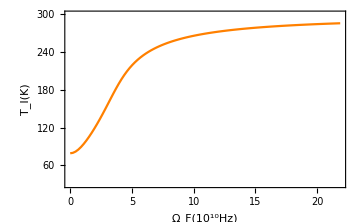
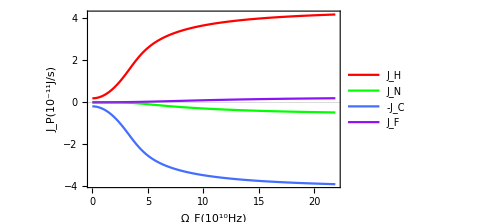
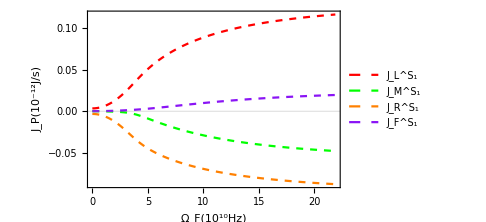
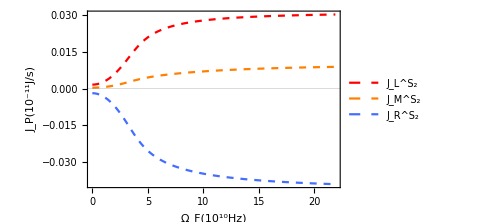

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Ω1min,Ω1max,Ω1res},
ωL1=0 ωconv;ωM1=0.1 ωconv;ωR1=0 ωconv;ωLM1=1 ωconv;ωMR1=1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;Tcnt= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotEngyFlowsWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Ω1min,Ω1max,Ω1res,True]
]
combFlowGraph2=%[[2]];
```

For comparison, a single temperature-controlled quantum thermal transistor

```mathematica
PlotEngyFlowsWithΩSingle[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ωmin_,Ωmax_,Ωres_,legends_]:=Module[{tempx,tempy,singleflows},
tempx=10^-10/(2π)Table[{Ω,Ω,Ω,Ω},{Ω,Ωmin,Ωmax,Ωres}];
tempy=10^11 Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
singleflows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,3,i]]}],{i,1,4}];
ListPlot[singleflows,
	ImageSize->Medium,
	PlotRange->{Automatic,Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["-J_C",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_F",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed},{RGBColor[0.5411,0.0784,0.9607],Dashed}},
	Joined->True]
]
```

```mathematica
PlotEngyFlowsWithΩSingle[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ωmin_,Ωmax_,Ωres_,legends_]:=Module[{tempx,tempy,singleflows},
tempx=Table[{Ω,Ω,Ω,Ω},{Ω,Ωmin,Ωmax,Ωres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
singleflows=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,3,i]]}],{i,1,4}];
ListPlot[singleflows,
	ImageSize->Medium,
	PlotLabel->"Single transistor - Heat flows",
	PlotRange->{Automatic,Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{Style["Ω_F"],Style["J_P"]},
	GridLines->{None,{0}},
	PlotLegends->legends &&{Style["J_H"],Style["J_N"],Style["-J_C"],Style["J_F"]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed},{RGBColor[0.5411,0.0784,0.9607],Dashed}},	
	Joined->True]
]
```

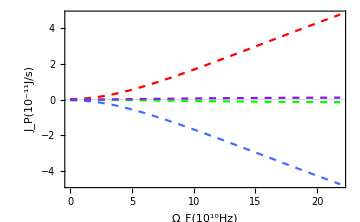

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres},
ωL=0 ωconv;ωM=0.1ωconv;ωR=0 ωconv;ωLM=1.0ωconv;ωMR=1.0ωconv;ωRL=0ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyFlowsWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres,False]
]
singlFlowGraph2=%;
```

Plotting the two graphs on top of each other

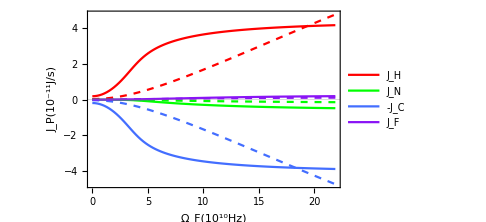

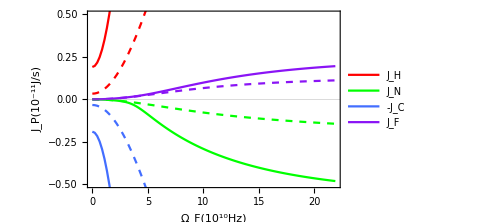

```mathematica
Show[combFlowGraph2,singlFlowGraph2,PlotRange->Full]
Show[combFlowGraph2,singlFlowGraph2,PlotRange->{-.5,.5}]
```

### Amplification factors

Amplification factor of the thermal optical gating action is given by the ratio α_Op=ΔJ_H/ΔJ_F

```mathematica
PlotAmplificationWithΩ[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Ω1min_,Ω1max_,Ω1res_]:=Module[{tempx,tempy,ampl,tempJH,tempJF,tempampl},
tempx=10^-10/(2π)Table[Ω1,{Ω1,Ω1min,Ω1max-Ω1res,Ω1res}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Ω1,Ω1min,Ω1max,Ω1res}];
tempJH=tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]];
tempJF=tempy[[;;,2,1,3,4]];
tempampl=Differences[tempJH]/Differences[tempJF];
ampl=MapThread[List,{tempx,tempampl}];
ListPlot[ampl,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ω1min,Ω1max},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->15],
		Style["α_Op = ΔJ_H/ΔJ_F",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},	
	PlotStyle->{Black},
	Joined->True]
]
```

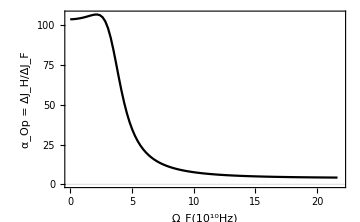

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Ω1min,Ω1max,Ω1res},
ωL1=0 ωconv;ωM1=0.1 ωconv;ωR1=0 ωconv;ωLM1=1 ωconv;ωMR1=1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;Tcnt= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotAmplificationWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Ω1min,Ω1max,Ω1res]
]
combAmplGraph2=%;
```

```mathematica
PlotAmplificationWithΩSingle[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ωmin_,Ωmax_,Ωres_]:=Module[{tempx,tempy,tempJH,tempJF,tempampl,singleeffic},
tempx=10^-10/(2π)Table[Ω,{Ω,Ωmin,Ωmax-Ωres,Ωres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
tempJH=tempy[[;;,3,1]];
tempJF=tempy[[;;,3,4]];
tempampl=Differences[tempJH]/Differences[tempJF];
singleeffic=MapThread[List,{tempx,tempampl}];
ListPlot[singleeffic,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ωmin,Ωmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->15],
		Style["α_Op = ΔJ_H/ΔJ_F",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{{Black,Dashed}},
	Joined->True]
]
```

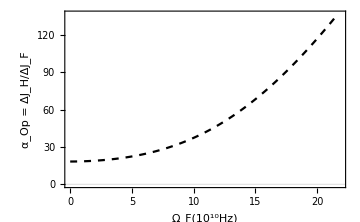

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres},
ωL=0 ωconv;ωM=0.1ωconv;ωR=0 ωconv;ωLM=1.0ωconv;ωMR=1.0ωconv;ωRL=0ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotAmplificationWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres]
]
singlAmplGraph2=%;
```

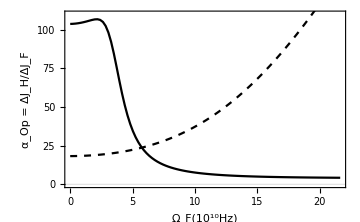

```mathematica
Show[combAmplGraph2,singlAmplGraph2,PlotRange->{Full,{0,110}}]
```

### Thermal efficiency

Energy efficiency of the thermal transistor action is given by the ratio β_Op=J_H/J_F

```mathematica
PlotEngyEfficiencyWithΩ[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Ω1min_,Ω1max_,Ω1res_]:=Module[{tempx,tempy,tempJH,tempJF,effic},
tempx=10^-10/(2π)Table[Ω1,{Ω1,Ω1min,Ω1max,Ω1res}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Ω1,Ω1min,Ω1max,Ω1res}];
tempJH=tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]];
tempJF=tempy[[;;,2,1,3,4]];
effic=MapThread[List,{tempx,tempJH/tempJF}];
ListPlot[effic,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ω1min,Ω1max},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->15],
		Style["β_Op = J_H/J_N",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{Black},
	Joined->True]
]
```

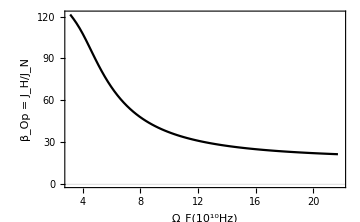

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Ω1min,Ω1max,Ω1res},
ωL1=0 ωconv;ωM1=0.1 ωconv;ωR1=0 ωconv;ωLM1=1 ωconv;ωMR1=1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;Tcnt= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
Ω1min=0.001ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotEngyEfficiencyWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Ω1min,Ω1max,Ω1res]
]
combEfficGraph2=%;
```

```mathematica
PlotEngyEfficiencyWithΩSingle[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ωmin_,Ωmax_,Ωres_]:=Module[{tempx,tempy,tempJH,tempJF,singleeffic},
tempx=10^-10/(2π)Table[Ω,{Ω,Ωmin,Ωmax,Ωres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
tempJH=tempy[[;;,3,1]];
tempJF=tempy[[;;,3,4]];
singleeffic=MapThread[List,{tempx,tempJH/tempJF}];
ListPlot[singleeffic,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ωmin,Ωmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->15],
		Style["β_Op = J_H/J_F",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{{Black,Dashed}},
	Joined->True]
]
```

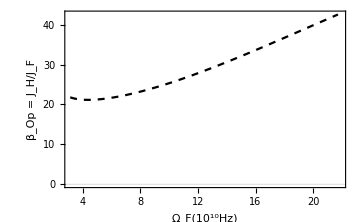

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres},
ωL=0 ωconv;ωM=0.1ωconv;ωR=0 ωconv;ωLM=1.0ωconv;ωMR=1.0ωconv;ωRL=0ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Ωmin=0.001ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyEfficiencyWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres]
]
singlEfficGraph2=%;
```

Plotting the two graphs on top of each other

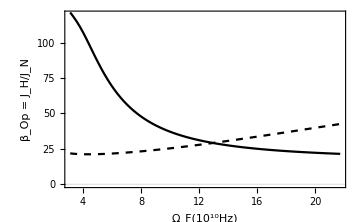

```mathematica
Show[combEfficGraph2,singlEfficGraph2,PlotRange->{Full,{0,120}}]
```

### Sensitivity to the optical field

Sensitivity of the thermal transistor action to changes in the optical field strength is given by the ratio η_Op^P=ΔJ_P/ΔΩ

```mathematica
PlotSensitivityWithΩ[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ω2_,Ω1min_,Ω1max_,Ω1res_,legends_]:=Module[{tempx,tempy,tempJH,tempJN,tempJC,tempJF,sensi},
tempx=10^-10/(2π)Table[Ω1,{Ω1,Ω1min,Ω1max-Ω1res,Ω1res}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,unitassum],{Ω1,Ω1min,Ω1max,Ω1res}];
tempJH=tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]];
tempJN=tempy[[;;,2,1,3,2]];
tempJC=tempy[[;;,2,2,3,3]];
tempJF=tempy[[;;,2,1,3,4]];
sensi={
	MapThread[List,{tempx,10^23 1/Ω1res Differences[tempJH]}],
	MapThread[List,{tempx,10^23 1/Ω1res Differences[tempJN]}],
	MapThread[List,{tempx,10^23 1/Ω1res Differences[tempJC]}],
	MapThread[List,{tempx,10^23 1/Ω1res Differences[tempJF]}]
};
ListPlot[sensi,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ω1min,Ω1max},Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-23η_Op^P",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["η_Op^H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["η_Op^N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["-η_Op^C",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["η_Op^F",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]},{RGBColor[0.2627,0.4313,1]},{RGBColor[0.5411,0.0784,0.9607]}},
	Joined->True]
]
```

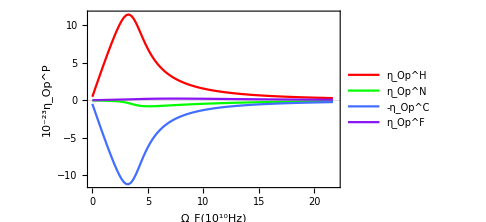

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Ω1min,Ω1max,Ω1res},
ωL1=0 ωconv;ωM1=0.1 ωconv;ωR1=0 ωconv;ωLM1=1 ωconv;ωMR1=1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Ω2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;Tcnt= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00007ωconv;
PlotSensitivityWithΩ[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω2,Ω1min,Ω1max,Ω1res,True]
]
sensiGraph2=%;
```

```mathematica
PlotSensitivityWithΩSingle[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κcol_,ωL_,ωM_,ωR_,ωLM_,ωMR_,ωRL_,Ωmin_,Ωmax_,Ωres_,legends_]:=Module[{tempx,tempy,tempJH,tempJN,tempJC,tempJF,singlesensi},
tempx=10^-10/(2π)Table[Ω,{Ω,Ωmin,Ωmax-Ωres,Ωres}];
tempy=Table[Subscript[varFunc, 1][Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
tempJH=tempy[[;;,3,1]];
tempJN=tempy[[;;,3,2]];
tempJC=tempy[[;;,3,3]];
tempJF=tempy[[;;,3,4]];
singlesensi={
	MapThread[List,{tempx,10^23 1/Ωres Differences[tempJH]}],
	MapThread[List,{tempx,10^23 1/Ωres Differences[tempJN]}],
	MapThread[List,{tempx,10^23 1/Ωres Differences[tempJC]}],
	MapThread[List,{tempx,10^23 1/Ωres Differences[tempJF]}]
};
ListPlot[singlesensi,
	ImageSize->Medium,
	PlotRange->{Full,Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-23η_Op^P",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["η_Op^H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["η_Op^N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["-η_Op^C",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["η_Op^F",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{RGBColor[1,0,0],Dashed},{RGBColor[0,1,0],Dashed},{RGBColor[0.2627,0.4313,1],Dashed},{RGBColor[0.5411,0.0784,0.9607],Dashed}},
	Joined->True]
]
```

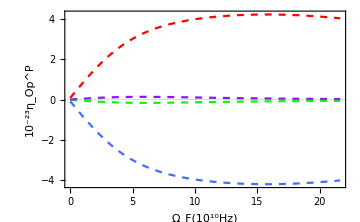

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres},
ωL=0 ωconv;ωM=0.1ωconv;ωR=0 ωconv;ωLM=1.0ωconv;ωMR=1.0ωconv;ωRL=0ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotSensitivityWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres,False]
]
singlSensiGraph2=%;
```

Plotting the two graphs on top of each other

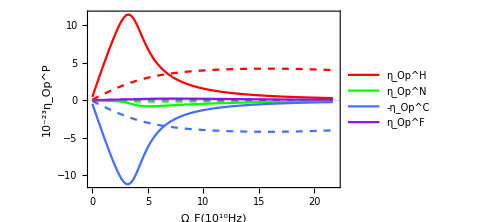

```mathematica
Show[sensiGraph2,singlSensiGraph2]
```

## Extra - Both optically-controlled transistors

### Absolute thermal flows

Similar to the above case, but now both transistors experience the same optical field. The system parameters of both must agree to the resonance condition with ω_F.

```mathematica
PlotEngyFlowsWithΩDual[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κint_,κcol_,ωL1_,ωM1_,ωR1_,ωLM1_,ωMR1_,ωRL1_,ωL2_,ωM2_,ωR2_,ωLM2_,ωMR2_,ωRL2_,Ωmin_,Ωmax_,Ωres_,legends_]:=Module[{tempx,tempy,tran1flows,tran2flows,inttemps,combflows},
tempx=10^-10/(2π)Table[{Ω,Ω,Ω,Ω},{Ω,Ωmin,Ωmax,Ωres}];
tempy=Table[combinedVarFunc[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,Ω,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ω,unitassum],{Ω,Ωmin,Ωmax,Ωres}];
tran1flows=Table[MapThread[List,{tempx[[;;,i]],10^11 tempy[[;;,2,1,3,i]]}],{i,1,4}];
tran2flows=Table[MapThread[List,{tempx[[;;,i]],10^11 tempy[[;;,2,2,3,i]]}],{i,1,3}];
inttemps=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,1]]}],{i,1,1}];
combflows={
	MapThread[List,{tempx[[;;,1]],10^11(tempy[[;;,2,1,3,1]]+tempy[[;;,2,2,3,1]])}],
	MapThread[List,{tempx[[;;,2]],10^11 tempy[[;;,2,1,3,2]]}],
	MapThread[List,{tempx[[;;,3]],10^11 tempy[[;;,2,2,3,3]]}],
	MapThread[List,{tempx[[;;,4]],10^11 tempy[[;;,2,1,3,4]]}]
};
{
ListPlot[inttemps,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ωmin,Ωmax},Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["T_I(K)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	PlotStyle->{Orange},
	Joined->True],
ListPlot[combflows,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ωmin,Ωmax},Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["-J_C",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_F",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{Red},{Green},{BlueC},{PurpleC}},
	Joined->True],
ListPlot[tran1flows,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ωmin,Ωmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_L^S_1",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_M^S_1",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_R^S_1",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_F^S_1",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{Red,Dashed},{Green,Dashed},{Orange,Dashed},{PurpleC,Dashed}},
	Joined->True],
ListPlot[tran2flows,
	ImageSize->Medium,
	PlotRange->{10^-10/(2π){Ωmin,Ωmax},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F(10^10Hz)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotLegends->legends &&{
		Style["J_L^S_2",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_M^S_2",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_R^S_2",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{{Red,Dashed},{Orange,Dashed},{BlueC,Dashed}},
	Joined->True]
}]
```

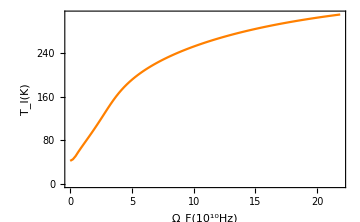
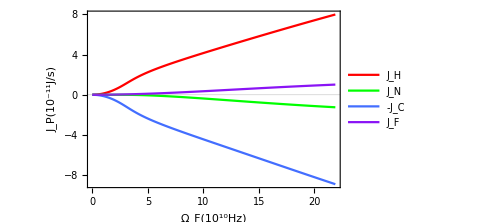
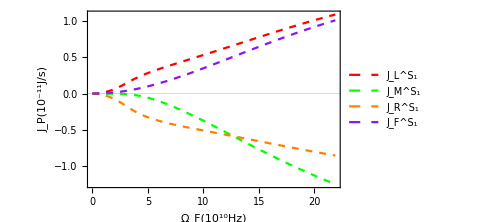
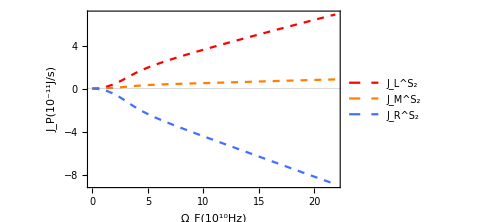

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ωmin,Ωmax,Ωres},
ωL1=0 ωconv;ωM1=0 ωconv;ωR1=0 ωconv;ωLM1=0.9 ωconv;ωMR1=1.1 ωconv;ωRL1=0ωconv;
ωL2=0 ωconv;ωM2=0ωconv;ωR2=0 ωconv;ωLM2=0.9 ωconv;ωMR2=1.1 ωconv;ωRL2=0ωconv;
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;Tcnt= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;κint=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyFlowsWithΩDual[Thot,Tcnt,Tcol,κhot,κcnt,κint,κcol,ωL1,ωM1,ωR1,ωLM1,ωMR1,ωRL1,ωL2,ωM2,ωR2,ωLM2,ωMR2,ωRL2,Ωmin,Ωmax,Ωres,True]
]
combFlowGraph3=%[[2]];
```

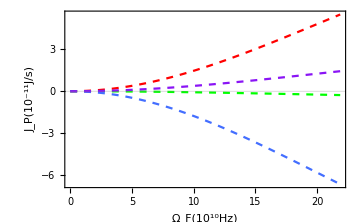

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres},
ωL=0 ωconv;ωM=0 ωconv;ωR=0 ωconv;ωLM=0.9ωconv;ωMR=1.1 ωconv;ωRL=0ωconv;
Thot= 0.2 Tconv;Tcnt=0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcol=0.01;κcnt=0.01;
Ωmin=0ωconv;Ωmax=0.007ωconv;Ωres=0.00007ωconv;
PlotEngyFlowsWithΩSingle[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωL,ωM,ωR,ωLM,ωMR,ωRL,Ωmin,Ωmax,Ωres,False]
]
singlFlowGraph3=%;
```

Plotting the two graphs on top of each other

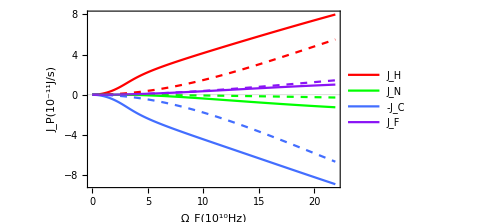

```mathematica
Show[combFlowGraph3,singlFlowGraph3,PlotRange->Full]
```

## Time dependent behaviors

### Darlington pair system

The function for time dependent temperature

```mathematica
timeassum:={
Ωcnt-> Piecewise[{{Ωcnt1,t<t0},{Ωcnt2,t>t0}}],
Ωcnt1->0.000ωconv,
Ωcnt2->0.005 ωconv
};
```

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
sysassum={
Subscript[ωL, 1]->0 ωconv,Subscript[ωM, 1]->0.1 ωconv,Subscript[ωR, 1]->0 ωconv,Subscript[ωLM, 1]->1.0ωconv,Subscript[ωMR, 1]->1.0ωconv,Subscript[ωRL, 1]->0ωconv,
Subscript[ωL, 2]->0 ωconv,Subscript[ωM, 2]->0 ωconv,Subscript[ωR, 2]->0 ωconv,Subscript[ωLM, 2]->0.9 ωconv,Subscript[ωMR, 2]->1.1ωconv,Subscript[ωRL, 2]->0ωconv,
Subscript[Ω, 1]->Ωcnt,Subscript[Ω, 2]->0ωconv,
Thot-> 0.2 Tconv,Tcol-> 0.02Tconv,Tcnt->0.02 Tconv,
κhot->0.01,κcol->0.01,κcnt->0.01,κint->0.01,
mCint->20mCconv
};
```

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the third are zero (ground/lowest energy state).

```mathematica
tmax=(25000/(Subscript[ωMR, 1] κhot))//.Flatten[{unitassum,sysassum}];
t0=0.25(25000/(Subscript[ωMR, 1] κhot))//.Flatten[{unitassum,sysassum}];
```

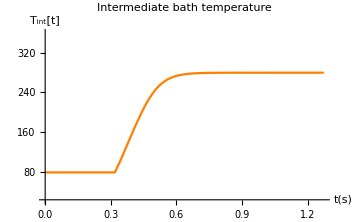

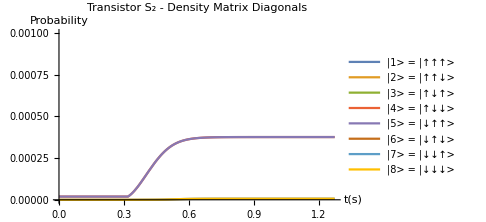

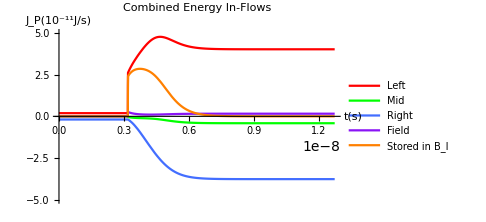

```mathematica
motioneqs={Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,timeassum,Jassum,NBEassum,Tassum}];
initconditions={Tint[-10tmax]==Tcol,Table[Subscript[ρ, S,i,j][-10tmax]==S,1(i,j i,3 1)+S,2(i,j i,3 0.5+i,j i,6 0.5),{S,1,2},{i,1,8},{j,1,8}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,8},{j,1,8}],Tint}],{t,-10tmax,tmax}
];

Tint[t]/.dynamics;
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Intermediate bath temperature"],
	PlotRange-> {0.8Tcol/.sysassum,1.2Thot/.sysassum},
	AxesLabel->{Style["t(s)"],Style["T_int[t]"]},
	PlotStyle->{Orange}
]

Flatten[{Table[Subscript[ρ, 2,i,i][t],{i,1,8}]}/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals"],
	PlotRange-> {0.0,0.001},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}]


Flatten[10^11{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2])
}//.Flatten[{unitassum,ωassum,ωassum1,timeassum,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
timedom=Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Combined Energy In-Flows"],
	PlotRange->{Automatic, {-5,5}},
	AxesLabel->{"t(s)","J_P(10^-11J/s)"},
	PlotLegends->{"Left ","Mid","Right","Field","Stored in B_I"},
	PlotStyle->{Red,Green,BlueC,PurpleC,Orange}]
```

-Graphics-

-Graphics-

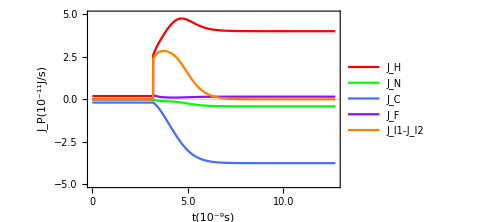

```mathematica
motioneqs={Subscript[motioneq, 1],Subscript[motioneq, 2],motioneqintbath}//.Flatten[{unitassum,ωassum,ωassum1,sysassum,timeassum,Jassum,NBEassum,Tassum}];
initconditions={Tint[-10tmax]==Tcol,Table[Subscript[ρ, S,i,j][-10tmax]==S,1(i,j i,3 1)+S,2(i,j i,3 0.5+i,j i,6 0.5),{S,1,2},{i,1,8},{j,1,8}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, S,i,j],{S,1,2},{i,1,8},{j,1,8}],Tint}],{t,-10tmax,tmax}
];

Tint[t]/.dynamics;
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Intermediate bath temperature"],
	PlotRange-> {0.8Tcol/.sysassum,1.2Thot/.sysassum},
	AxesLabel->{Style["t(s)"],Style["T_int[t]"]},
	PlotStyle->{Orange}
]

Flatten[{Table[Subscript[ρ, 2,i,i][t],{i,1,8}]}/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Transistor S_2 - Density Matrix Diagonals"],
	PlotRange-> {0.0,0.001},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}]


Flatten[10^11{
Subscript[EngyFlowIn, 1,1]+Subscript[EngyFlowIn, 2,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 2,3],Subscript[EngyFlowInField, 1]+Subscript[EngyFlowInField, 2],-(Subscript[EngyFlowIn, 1,3]+Subscript[EngyFlowIn, 2,2])
}//.Flatten[{unitassum,ωassum,ωassum1,timeassum,sysassum,Jassum,NBEassum,Tassum}]/.dynamics];
timedom=Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotRange->{Automatic, {-5,5}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["t(10^-9s)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	FrameTicks->{Automatic,{Charting`FindTicks[{0,tmax},{0,tmax 10^9}],Automatic}},	
	GridLines->{None,{0}},
	PlotLegends->{
		Style["J_H",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_N",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_C",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_F",FontFamily->"Times New Roman",Bold,FontSize->16],
		Style["J_I1-J_I2",FontFamily->"Times New Roman",Bold,FontSize->16]},
	PlotStyle->{Red,Green,BlueC,PurpleC,Orange}]
```

### Single transistor system, for comparison

```mathematica
timeassum:={
Ωcnt-> Piecewise[{{Ωcnt1,t<t0},{Ωcnt2,t>t0}}],
Ωcnt1->0.000ωconv,
Ωcnt2->0.005 ωconv
};
```

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
indsysassum={
Subscript[T, 1,1]-> 0.2 Tconv,Subscript[T, 1,2]-> 0.02 Tconv,Subscript[T, 1,3]-> 0.02 Tconv,
Subscript[κ, 1,1]-> 0.01,Subscript[κ, 1,2]-> 0.01,Subscript[κ, 1,3]-> 0.01,
Subscript[ωL, 1]->0 ωconv,Subscript[ωM, 1]->0.1 ωconv,Subscript[ωR, 1]->0 ωconv,Subscript[ωLM, 1]-> 1.0ωconv,Subscript[ωMR, 1]->1.0 ωconv,Subscript[ωRL, 1]->0ωconv,
Subscript[Ω, 1]->Ωcnt
};
```

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the third are zero (ground/lowest energy state).

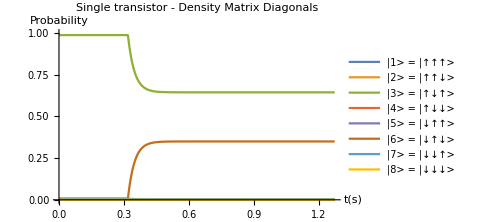

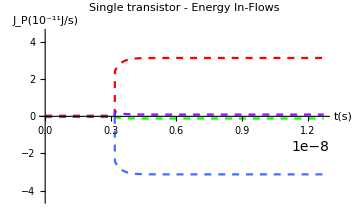

```mathematica
motioneqs=Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,timeassum}];
initconditions={Table[Subscript[ρ, 1,i,j][-10tmax]==i,j i,3 1,{i,1,8},{j,1,8}]}/.sysassum;

singdynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,8},{j,1,8}]}],{t,-10tmax,tmax}
];

Flatten[{Table[Subscript[ρ, 1,i,i][t],{i,1,8}]}/.singdynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Single transistor - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}]

Flatten[10^11{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum,timeassum}]/.singdynamics];
singtimedom=Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Single transistor - Energy In-Flows"],
	PlotRange->{Automatic,{-4.5,4.5}},
	AxesLabel->{"t(s)","J_P(10^-11J/s)"},
	PlotStyle->{{Red,Dashed},{Green,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}]
```

-Graphics-

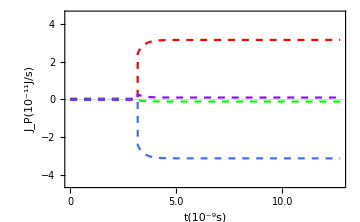

```mathematica
motioneqs=Subscript[motioneq, 1]//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,timeassum}];
initconditions={Table[Subscript[ρ, 1,i,j][-10tmax]==i,j i,3 1,{i,1,8},{j,1,8}]}/.sysassum;

singdynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[{Table[Subscript[ρ, 1,i,j],{i,1,8},{j,1,8}]}],{t,-10tmax,tmax}
];

Flatten[{Table[Subscript[ρ, 1,i,i][t],{i,1,8}]}/.singdynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Single transistor - Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1> = |↑↑↑> "],Style["|2> = |↑↑↓> "],Style["|3> = |↑↓↑> "],Style["|4> = |↑↓↓> "],
		Style["|5> = |↓↑↑> "],Style["|6> = |↓↑↓> "],Style["|7> = |↓↓↑> "],Style["|8> = |↓↓↓> "]}]

Flatten[10^11{
Subscript[EngyFlowIn, 1,1],Subscript[EngyFlowIn, 1,2],Subscript[EngyFlowIn, 1,3],Subscript[EngyFlowInField, 1]
}//.Flatten[{unitassum,ωassum,ωassum1,indsysassum,Jassum,NBEassum,Tassum,timeassum}]/.singdynamics];
singtimedom=Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotRange->{Automatic,{-4.5,4.5}},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["t(10^-9s)",FontFamily->"Times New Roman",FontSize->16],
		Style["J_P(10^-11J/s)",FontFamily->"Times New Roman",FontSize->16]},
	FrameTicks->{Automatic,{Charting`FindTicks[{0,tmax},{0,tmax 10^9}],Automatic}},
	FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{{Red,Dashed},{Green,Dashed},{BlueC,Dashed},{PurpleC,Dashed}}]
```

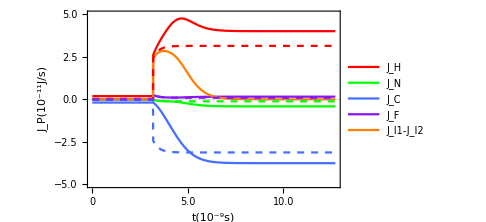

```mathematica
Show[timedom,singtimedom]
```